## Derivation of R_m

For two hosts, the general model, given by equations (5-11) in the main text, is:

```mathematica
(* Dynamics of susceptible individuals of host species 1*)
dS1dt=r1 (S1+I1s+D1ss+I1g+C1sg) (1-(S1+I1s+D1ss+I1g+C1sg)/K1)-βS1 S1 (P1+Pg);
(* Dynamics of individuals of host species 1 singly infected with its specialist parasite *)
dI1sdt=βS1 S1 P1-σD1 βI1 I1s P1-σC1 βI1 I1s Pg -μ1 I1s;
(* Dynamics of individuals of host species 1 doubly infected with its specialist parasite *)
dD1ssdt=σD1 βI1 I1s P1-μ1 D1ss;
(* Dynamics of the specialist parasite of host species 1 in the environment *)
dP1dt=λ1 (I1s+D1ss+x1 C1sg)-(βS1 S1+βI1 I1s+βD1 D1ss+βC1 C1sg) P1-γ P1; 

(* Dynamics of susceptible individuals of host species 2 *)
dS2dt=r2 (S2+I2s+D2ss+I2g+C2sg) (1-(S2+I2s+D2ss+I2g+C2sg)/K2)-βS2 S2 (P2+Pg);
(* Dynamics of individuals of host species 2 singly infected with its specialist parasite *)
dI2sdt=βS2 S2 P2-σD2 βI2 I2s P2-σC2 βI2 I2s Pg -μ2 I2s;
(* Dynamics of individuals of host species 2 doubly infected with its specialist parasite *)
dD2ssdt=σD2 βI2 I2s P2-μ2 D2ss;
(* Dynamics of the specialist parasite of host species 2 in the environment *)
dP2dt=λ2 (I2s+D2ss+x2 C2sg)-(βS2 S2+βI2 I2s+βD2 D2ss+βC2 C2sg) P2-γ P2; 

(* Dynamics of individuals of host species 1 singly infected with the generalist parasite *)
dI1gdt=βS1 S1 Pg-σC1 βI1 I1g P1-μ1 I1g;
(* Dynamics of individuals of host species 2 singly infected with the generalist parasite *)
dI2gdt=βS2 S2 Pg-σC2 βI2 I2g P2-μ2 I2g;
(* Dynamics of individuals of host species 1 coinfected with its specialist and the generalist parasite *)
dC1sgdt=σC1 βI1 (I1s Pg+I1g P1)-μ1 C1sg;
(* Dynamics of individuals of host species 2 coinfected with its specialist and the generalist parasite *)
dC2sgdt=σC2 βI2 (I2s Pg+I2g P2)-μ2 C2sg;
(* Dynamics of the generalist parasite in the environment *)
dPgdt=a λ1 (I1g+(1-x1) C1sg)+a λ2 (I2g+(1-x2) C2sg)-(βS1 S1+βI1 I1s+βD1 D1ss+βS2 S2+βI2 I2s+βD2 D2ss) Pg-γ Pg;
```

Whether the generalist parasite can invade will depend on the stability of the equilibrium 
(OverHat[S_1],OverHat[I_(1,s)],OverHat[D_(1,s,s)],OverHat[P_1],OverHat[S_2],OverHat[I_(2,s)],OverHat[D_(2,s,s)],OverHat[P_2],0,0,0,0,0). This can be evaluated by looking at the eigenvalues of the Jacobian matrix for the full system. The Jacobian matrix at this equilibrium has a simple block upper triangular structure: J=(J_1
0
00
J_2
0M_1
M_2
J_m), where J_1 is the submatrix that determines the stability of the (S_1,I_(1,s),D_(1,s,s),P_1) subsystem and J_2 is the submatrix that determines the stability of the (S_2,I_(2,s),D_(2,s,s),P_2) subsystem. J_m is the submatrix of partial derivatives involving the equations for the generalist. Because of its simple structure, the eigenvalues of the full system are given by the eigenvalues of the submatrices J_1, J_2 and J_m. Assuming that the (S_1,I_(1,s),D_(1,s,s),P_1) and  (S_2,I_(2,s),D_(2,s,s),P_2) subsystems are both stable, all of the eigenvalues of J_1 and J_2 are negative. Therefore, we are interested only in the eigenvalues of J_m.

```mathematica
(* Calculating the Jacobian matrix and evaluating it at the equilibrium where Subscript[I, 1,g]=Subscript[I, 2,g]=Subscript[C, 1,s,g]=Subscript[C, 2,s,g]=Subscript[P, g]=0 *)
J={{D[dS1dt,S1],D[dS1dt,I1s],D[dS1dt,D1ss],D[dS1dt,P1],
D[dS1dt,S2],D[dS1dt,I2s],D[dS1dt,D2ss],D[dS1dt,P2],
D[dS1dt,I1g],D[dS1dt,I2g],D[dS1dt,C1sg],D[dS1dt,C2sg],D[dS1dt,Pg]},
{D[dI1sdt,S1],D[dI1sdt,I1s],D[dI1sdt,D1ss],D[dI1sdt,P1],
D[dI1sdt,S2],D[dI1sdt,I2s],D[dI1sdt,D2ss],D[dI1sdt,P2],
D[dI1sdt,I1g],D[dI1sdt,I2g],D[dI1sdt,C1sg],D[dI1sdt,C2sg],D[dI1sdt,Pg]},
{D[dD1ssdt,S1],D[dD1ssdt,I1s],D[dD1ssdt,D1ss],D[dD1ssdt,P1],
D[dD1ssdt,S2],D[dD1ssdt,I2s],D[dD1ssdt,D2ss],D[dD1ssdt,P2],
D[dD1ssdt,I1g],D[dD1ssdt,I2g],D[dD1ssdt,C1sg],D[dD1ssdt,C2sg],D[dD1ssdt,Pg]},
{D[dP1dt,S1],D[dP1dt,I1s],D[dP1dt,D1ss],D[dP1dt,P1],
D[dP1dt,S2],D[dP1dt,I2s],D[dP1dt,D2ss],D[dP1dt,P2],
D[dP1dt,I1g],D[dP1dt,I2g],D[dP1dt,C1sg],D[dP1dt,C2sg],D[dP1dt,Pg]},
{D[dS2dt,S1],D[dS2dt,I1s],D[dS2dt,D1ss],D[dS2dt,P1],
D[dS2dt,S2],D[dS2dt,I2s],D[dS2dt,D2ss],D[dS2dt,P2],
D[dS2dt,I1g],D[dS2dt,I2g],D[dS2dt,C1sg],D[dS2dt,C2sg],D[dS2dt,Pg]},
{D[dI2sdt,S1],D[dI2sdt,I1s],D[dI2sdt,D1ss],D[dI2sdt,P1],
D[dI2sdt,S2],D[dI2sdt,I2s],D[dI2sdt,D2ss],D[dI2sdt,P2],
D[dI2sdt,I1g],D[dI2sdt,I2g],D[dI2sdt,C1sg],D[dI2sdt,C2sg],D[dI2sdt,Pg]},
{D[dD2ssdt,S1],D[dD2ssdt,I1s],D[dD2ssdt,D1ss],D[dD2ssdt,P1],
D[dD2ssdt,S2],D[dD2ssdt,I2s],D[dD2ssdt,D2ss],D[dD2ssdt,P2],
D[dD2ssdt,I1g],D[dD2ssdt,I2g],D[dD2ssdt,C1sg],D[dD2ssdt,C2sg],D[dD2ssdt,Pg]},
{D[dP2dt,S1],D[dP2dt,I1s],D[dP2dt,D1ss],D[dP2dt,P1],
D[dP2dt,S2],D[dP2dt,I2s],D[dP2dt,D2ss],D[dP2dt,P2],
D[dP2dt,I1g],D[dP2dt,I2g],D[dP2dt,C1sg],D[dP2dt,C2sg],D[dP2dt,Pg]},
{D[dI1gdt,S1],D[dI1gdt,I1s],D[dI1gdt,D1ss],D[dI1gdt,P1],
D[dI1gdt,S2],D[dI1gdt,I2s],D[dI1gdt,D2ss],D[dI1gdt,P2],
D[dI1gdt,I1g],D[dI1gdt,I2g],D[dI1gdt,C1sg],D[dI1gdt,C2sg],D[dI1gdt,Pg]},
{D[dI2gdt,S1],D[dI2gdt,I1s],D[dI2gdt,D1ss],D[dI2gdt,P1],
D[dI2gdt,S2],D[dI2gdt,I2s],D[dI2gdt,D2ss],D[dI2gdt,P2],
D[dI2gdt,I1g],D[dI2gdt,I2g],D[dI2gdt,C1sg],D[dI2gdt,C2sg],D[dI2gdt,Pg]},
{D[dC1sgdt,S1],D[dC1sgdt,I1s],D[dC1sgdt,D1ss],D[dC1sgdt,P1],
D[dC1sgdt,S2],D[dC1sgdt,I2s],D[dC1sgdt,D2ss],D[dC1sgdt,P2],
D[dC1sgdt,I1g],D[dC1sgdt,I2g],D[dC1sgdt,C1sg],D[dC1sgdt,C2sg],D[dC1sgdt,Pg]},
{D[dC2sgdt,S1],D[dC2sgdt,I1s],D[dC2sgdt,D1ss],D[dC2sgdt,P1],
D[dC2sgdt,S2],D[dC2sgdt,I2s],D[dC2sgdt,D2ss],D[dC2sgdt,P2],
D[dC2sgdt,I1g],D[dC2sgdt,I2g],D[dC2sgdt,C1sg],D[dC2sgdt,C2sg],D[dC2sgdt,Pg]},
{D[dPgdt,S1],D[dPgdt,I1s],D[dPgdt,D1ss],D[dPgdt,P1],
D[dPgdt,S2],D[dPgdt,I2s],D[dPgdt,D2ss],D[dPgdt,P2],
D[dPgdt,I1g],D[dPgdt,I2g],D[dPgdt,C1sg],D[dPgdt,C2sg],D[dPgdt,Pg]}}/.{I1g->0,I2g->0,C1sg->0,C2sg->0,Pg->0};
(* The submatrices *)
(* J1 *)
MatrixForm[J1=J[[1;;4,1;;4]]]
```

(-(r1 (D1ss+I1s+S1))/K1+r1 (1-(D1ss+I1s+S1)/K1)-P1 βS1 | -(r1 (D1ss+I1s+S1))/K1+r1 (1-(D1ss+I1s+S1)/K1) | -(r1 (D1ss+I1s+S1))/K1+r1 (1-(D1ss+I1s+S1)/K1) | -S1 βS1
P1 βS1 | -μ1-P1 βI1 σD1 | 0 | S1 βS1-I1s βI1 σD1
0 | P1 βI1 σD1 | -μ1 | I1s βI1 σD1
-P1 βS1 | -P1 βI1+λ1 | -P1 βD1+λ1 | -D1ss βD1-I1s βI1-S1 βS1-γ)

```mathematica
(* Zeros *)
MatrixForm[J[[1;;4,5;;8]]]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
(* M1 *)
MatrixForm[M1=J[[1;;4,9;;13]]]
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -I1s βI1 σC1
0 | 0 | 0 | 0 | 0
0 | 0 | -P1 βC1+x1 λ1 | 0 | 0)

```mathematica
(* Zeros *)
MatrixForm[J[[5;;8,1;;4]]]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
(* J2 *)
MatrixForm[J2=J[[5;;8,5;;8]]]
```

(-(r2 (D2ss+I2s+S2))/K2+r2 (1-(D2ss+I2s+S2)/K2)-P2 βS2 | -(r2 (D2ss+I2s+S2))/K2+r2 (1-(D2ss+I2s+S2)/K2) | -(r2 (D2ss+I2s+S2))/K2+r2 (1-(D2ss+I2s+S2)/K2) | -S2 βS2
P2 βS2 | -μ2-P2 βI2 σD2 | 0 | S2 βS2-I2s βI2 σD2
0 | P2 βI2 σD2 | -μ2 | I2s βI2 σD2
-P2 βS2 | -P2 βI2+λ2 | -P2 βD2+λ2 | -D2ss βD2-I2s βI2-S2 βS2-γ)

```mathematica
(* M2 *)
MatrixForm[M2=J[[5;;8,9;;13]]]
```

(0 | -(r2 (D2ss+I2s+S2))/K2+r2 (1-(D2ss+I2s+S2)/K2) | 0 | -(r2 (D2ss+I2s+S2))/K2+r2 (1-(D2ss+I2s+S2)/K2) | -S2 βS2
0 | 0 | 0 | 0 | -I2s βI2 σC2
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -P2 βC2+x2 λ2 | 0)

```mathematica
(* Zeros *)
MatrixForm[J[[9;;13,1;;4]]]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
(* Zeros *)
MatrixForm[J[[9;;13,5;;8]]]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
(* Jm *)
MatrixForm[Jm=J[[9;;13,9;;13]]]
```

(-μ1-P1 βI1 σC1 | 0 | 0 | 0 | S1 βS1
0 | -μ2-P2 βI2 σC2 | 0 | 0 | S2 βS2
P1 βI1 σC1 | 0 | -μ1 | 0 | I1s βI1 σC1
0 | P2 βI2 σC2 | 0 | -μ2 | I2s βI2 σC2
a λ1 | a λ2 | a (1-x1) λ1 | a (1-x2) λ2 | -D1ss βD1-D2ss βD2-I1s βI1-I2s βI2-S1 βS1-S2 βS2-γ)

The submatrix J_m=(-μ_1-σ_C_1 β_I_1 OverHat[P_1] | 0 | 0 | 0 | β_S_1 OverHat[S_1]
0 | -μ_2-σ_C_2 β_I_2 OverHat[P_2] | 0 | 0 | β_S_2 OverHat[S_2]
σ_C_1 β_I_1 OverHat[P_1] | 0 | -μ1 | 0 | σ_C_1 β_I_1 OverHat[I_(1,s)]
0 | σ_C_2 β_I_2 OverHat[P_2] | 0 | -μ2 | σ_C_2 β_I_2 OverHat[I_(2,s)]
a λ_1 | a λ_2 | a (1-x_1) λ_1 | a (1-x_2) λ_2 | -β_S_1 OverHat[S_1]-β_S_2 OverHat[S_2]-β_I_1 OverHat[I_(1,s)]-β_I_2 OverHat[I_(2,s)]-β_D_1 OverHat[D_(1,s,s)]-β_D_2 OverHat[D_(2,s,s)]-γ).
Rather than finding for the eigenvalues of this submatrix, we make use of the Next Generation Theorem and rewrite J_m as F-V, where F=(0 | 0 | 0 | 0 | β_S_1 OverHat[S_1]
0 | 0 | 0 | 0 | β_S_2 OverHat[S_2]
σ_C_1 β_I_1 OverHat[P_1] | 0 | 0 | 0 | σ_C_1 β_I_1 OverHat[I_(1,s)]
0 | σ_C_2 β_I_2 OverHat[P_2] | 0 | 0 | σ_C_2 β_I_2 OverHat[I_(2,s)]
0 | 0 | 0 | 0 | 0) and V=(μ_1+σ_C_1 β_I_1 OverHat[P_1] | 0 | 0 | 0 | 0
0 | μ_2+σ_C_2 β_I_2 OverHat[P_2] | 0 | 0 | 0
0 | 0 | μ1 | 0 | 0
0 | 0 | 0 | μ2 | 0
-a λ_1 | -a λ_2 | -a (1-x_1) λ_1 | -a (1-x_2) λ_2 | β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+β_I_2 OverHat[I_(2,s)]+β_D_1 OverHat[D_(1,s,s)]+β_D_2 OverHat[D_(2,s,s)]+γ)

```mathematica
F={{0,0,0,0,S1 βS1},{0,0,0,0,S2 βS2},{P1 βI1 σC1,0,0,0,I1s βI1 σC1},{0,P2 βI2 σC2,0,0,I2s βI2 σC2},{0,0,0,0,0}};
V={{μ1+P1 βI1 σC1,0,0,0,0},{0,μ2+P2 βI2 σC2,0,0,0},{0,0,μ1,0,0},{0,0,0,μ2,0},{-a λ1,-a λ2,-a (1-x1) λ1,-a (1-x2) λ2,D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ}};
Jm==F-V
```

True

The Next Generation Theorem states that, if a matrix J can be written J=F-V, where F≥0, V^-1≥ 0 and all of the eigenvalues of -V are negative, then the dominant eigenvalue of J will be greater than zero whenever the spectral radius of F.V^-1>1. Note that the spectral radius largest real part of all of the eigenvalues.

```mathematica
(* Verifying that all elements of V^-1≥0*)
Inverse[V]//Simplify
```

{{1/(μ1+P1 βI1 σC1),0,0,0,0},{0,1/(μ2+P2 βI2 σC2),0,0,0},{0,0,1/μ1,0,0},{0,0,0,1/μ2,0},{(a λ1)/((D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) (μ1+P1 βI1 σC1)),(a λ2)/((D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) (μ2+P2 βI2 σC2)),-((a (-1+x1) λ1)/((D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1)),-((a (-1+x2) λ2)/((D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ2)),1/(D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ)}}

```mathematica
(* Verifying that all eigenvalues of -V<0 *)
Eigenvalues[-V]//Simplify
```

{-D1ss βD1-D2ss βD2-I1s βI1-I2s βI2-S1 βS1-S2 βS2-γ,-μ1,-μ2,-μ1-P1 βI1 σC1,-μ2-P2 βI2 σC2}

```mathematica
(* Eigenvalues of F.V^-1 *)
```

```mathematica
Eigenvalues[Dot[F,Inverse[V]]]//Simplify
```

{0,0,0,(a S2 βS2 λ2 μ1^2 μ2+a S1 βS1 λ1 μ1 μ2^2+a P1 S2 βI1 βS2 λ2 μ1 μ2 σC1+a I1s βI1 λ1 μ1 μ2^2 σC1-a I1s x1 βI1 λ1 μ1 μ2^2 σC1+a I1s P1 βI1^2 λ1 μ2^2 σC1^2-a I1s P1 x1 βI1^2 λ1 μ2^2 σC1^2+a P2 S1 βI2 βS1 λ1 μ1 μ2 σC2+a I2s βI2 λ2 μ1^2 μ2 σC2-a I2s x2 βI2 λ2 μ1^2 μ2 σC2+a I1s P2 βI1 βI2 λ1 μ1 μ2 σC1 σC2-a I1s P2 x1 βI1 βI2 λ1 μ1 μ2 σC1 σC2+a I2s P1 βI1 βI2 λ2 μ1 μ2 σC1 σC2-a I2s P1 x2 βI1 βI2 λ2 μ1 μ2 σC1 σC2+a I1s P1 P2 βI1^2 βI2 λ1 μ2 σC1^2 σC2-a I1s P1 P2 x1 βI1^2 βI2 λ1 μ2 σC1^2 σC2+a I2s P2 βI2^2 λ2 μ1^2 σC2^2-a I2s P2 x2 βI2^2 λ2 μ1^2 σC2^2+a I2s P1 P2 βI1 βI2^2 λ2 μ1 σC1 σC2^2-a I2s P1 P2 x2 βI1 βI2^2 λ2 μ1 σC1 σC2^2-√(a (-4 (D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2) (P2 S2 (-1+x2) βI2 βS2 λ2 μ1^2 σC2+P1 βI1 σC1 (P2 S2 (-1+x2) βI2 βS2 λ2 μ1 σC2+S1 (-1+x1) βS1 λ1 μ2 (μ2+P2 βI2 σC2)))+a (S2 βS2 λ2 μ1 μ2 (μ1+P1 βI1 σC1)+(μ2+P2 βI2 σC2) (S1 βS1 λ1 μ1 μ2-(μ1+P1 βI1 σC1) (I1s (-1+x1) βI1 λ1 μ2 σC1+I2s (-1+x2) βI2 λ2 μ1 σC2)))^2)))/(2 (D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2)),(a S2 βS2 λ2 μ1^2 μ2+a S1 βS1 λ1 μ1 μ2^2+a P1 S2 βI1 βS2 λ2 μ1 μ2 σC1+a I1s βI1 λ1 μ1 μ2^2 σC1-a I1s x1 βI1 λ1 μ1 μ2^2 σC1+a I1s P1 βI1^2 λ1 μ2^2 σC1^2-a I1s P1 x1 βI1^2 λ1 μ2^2 σC1^2+a P2 S1 βI2 βS1 λ1 μ1 μ2 σC2+a I2s βI2 λ2 μ1^2 μ2 σC2-a I2s x2 βI2 λ2 μ1^2 μ2 σC2+a I1s P2 βI1 βI2 λ1 μ1 μ2 σC1 σC2-a I1s P2 x1 βI1 βI2 λ1 μ1 μ2 σC1 σC2+a I2s P1 βI1 βI2 λ2 μ1 μ2 σC1 σC2-a I2s P1 x2 βI1 βI2 λ2 μ1 μ2 σC1 σC2+a I1s P1 P2 βI1^2 βI2 λ1 μ2 σC1^2 σC2-a I1s P1 P2 x1 βI1^2 βI2 λ1 μ2 σC1^2 σC2+a I2s P2 βI2^2 λ2 μ1^2 σC2^2-a I2s P2 x2 βI2^2 λ2 μ1^2 σC2^2+a I2s P1 P2 βI1 βI2^2 λ2 μ1 σC1 σC2^2-a I2s P1 P2 x2 βI1 βI2^2 λ2 μ1 σC1 σC2^2+√(a (-4 (D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2) (P2 S2 (-1+x2) βI2 βS2 λ2 μ1^2 σC2+P1 βI1 σC1 (P2 S2 (-1+x2) βI2 βS2 λ2 μ1 σC2+S1 (-1+x1) βS1 λ1 μ2 (μ2+P2 βI2 σC2)))+a (S2 βS2 λ2 μ1 μ2 (μ1+P1 βI1 σC1)+(μ2+P2 βI2 σC2) (S1 βS1 λ1 μ1 μ2-(μ1+P1 βI1 σC1) (I1s (-1+x1) βI1 λ1 μ2 σC1+I2s (-1+x2) βI2 λ2 μ1 σC2)))^2)))/(2 (D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2))}

The spectral bound condition is R_m=(β_S_1 OverHat[S_1])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+β_I_2 OverHat[I_(2,s)]+β_D_1 OverHat[D_(1,s,s)]+β_D_2 OverHat[D_(2,s,s)]+γ) (μ_1/(μ_1+σ_C_1 β_I_1 OverHat[P_1]) (a λ_1)/μ_1+(σ_C_1 β_I_1 OverHat[P_1])/(μ_1+σ_C_1 β_I_1 OverHat[P_1]) (a (1-x_1)λ_1)/μ_1)+(β_I_1 OverHat[I_(1,s)])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+β_I_2 OverHat[I_(2,s)]+β_D_1 OverHat[D_(1,s,s)]+β_D_2 OverHat[D_(2,s,s)]+γ)(a (1-x_1)λ_1)/μ_1+(β_S_2 OverHat[S_2])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+β_I_2 OverHat[I_(2,s)]+β_D_1 OverHat[D_(1,s,s)]+β_D_2 OverHat[D_(2,s,s)]+γ) (μ_2/(μ_2+σ_C_2 β_I_2 OverHat[P_2]) (a λ_2)/μ_2+(σ_C_2 β_I_2 OverHat[P_2])/(μ_2+σ_C_2 β_I_2 OverHat[P_2]) (a (1-x_2)λ_2)/μ_2)+(β_I_2 OverHat[I_(2,s)])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+β_I_2 OverHat[I_(2,s)]+β_D_1 OverHat[D_(1,s,s)]+β_D_2 OverHat[D_(2,s,s)]+γ)(a (1-x_2)λ_2)/μ_2 >1.

The generalized R_m expression for any number of hosts (Eq. 12 in the main text) follows from this expression.

```mathematica
(* The condition for instability of the generalist-free equilibrium is that the spectral bound > 1 *)
(a S2 βS2 λ2 μ1^2 μ2+a S1 βS1 λ1 μ1 μ2^2+a P1 S2 βI1 βS2 λ2 μ1 μ2 σC1+a I1s βI1 λ1 μ1 μ2^2 σC1-a I1s x1 βI1 λ1 μ1 μ2^2 σC1+a I1s P1 βI1^2 λ1 μ2^2 σC1^2-a I1s P1 x1 βI1^2 λ1 μ2^2 σC1^2+a P2 S1 βI2 βS1 λ1 μ1 μ2 σC2+a I2s βI2 λ2 μ1^2 μ2 σC2-a I2s x2 βI2 λ2 μ1^2 μ2 σC2+a I1s P2 βI1 βI2 λ1 μ1 μ2 σC1 σC2-a I1s P2 x1 βI1 βI2 λ1 μ1 μ2 σC1 σC2+a I2s P1 βI1 βI2 λ2 μ1 μ2 σC1 σC2-a I2s P1 x2 βI1 βI2 λ2 μ1 μ2 σC1 σC2+a I1s P1 P2 βI1^2 βI2 λ1 μ2 σC1^2 σC2-a I1s P1 P2 x1 βI1^2 βI2 λ1 μ2 σC1^2 σC2+a I2s P2 βI2^2 λ2 μ1^2 σC2^2-a I2s P2 x2 βI2^2 λ2 μ1^2 σC2^2+a I2s P1 P2 βI1 βI2^2 λ2 μ1 σC1 σC2^2-a I2s P1 P2 x2 βI1 βI2^2 λ2 μ1 σC1 σC2^2-√(a (-4 (D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2) (P2 S2 (-1+x2) βI2 βS2 λ2 μ1^2 σC2+P1 βI1 σC1 (P2 S2 (-1+x2) βI2 βS2 λ2 μ1 σC2+S1 (-1+x1) βS1 λ1 μ2 (μ2+P2 βI2 σC2)))+a (S2 βS2 λ2 μ1 μ2 (μ1+P1 βI1 σC1)+(μ2+P2 βI2 σC2) (S1 βS1 λ1 μ1 μ2-(μ1+P1 βI1 σC1) (I1s (-1+x1) βI1 λ1 μ2 σC1+I2s (-1+x2) βI2 λ2 μ1 σC2)))^2)))/(2 (D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2))>1;
(* Cross-multiplying *)
(a S2 βS2 λ2 μ1^2 μ2+a S1 βS1 λ1 μ1 μ2^2+a P1 S2 βI1 βS2 λ2 μ1 μ2 σC1+a I1s βI1 λ1 μ1 μ2^2 σC1-a I1s x1 βI1 λ1 μ1 μ2^2 σC1+a I1s P1 βI1^2 λ1 μ2^2 σC1^2-a I1s P1 x1 βI1^2 λ1 μ2^2 σC1^2+a P2 S1 βI2 βS1 λ1 μ1 μ2 σC2+a I2s βI2 λ2 μ1^2 μ2 σC2-a I2s x2 βI2 λ2 μ1^2 μ2 σC2+a I1s P2 βI1 βI2 λ1 μ1 μ2 σC1 σC2-a I1s P2 x1 βI1 βI2 λ1 μ1 μ2 σC1 σC2+a I2s P1 βI1 βI2 λ2 μ1 μ2 σC1 σC2-a I2s P1 x2 βI1 βI2 λ2 μ1 μ2 σC1 σC2+a I1s P1 P2 βI1^2 βI2 λ1 μ2 σC1^2 σC2-a I1s P1 P2 x1 βI1^2 βI2 λ1 μ2 σC1^2 σC2+a I2s P2 βI2^2 λ2 μ1^2 σC2^2-a I2s P2 x2 βI2^2 λ2 μ1^2 σC2^2+a I2s P1 P2 βI1 βI2^2 λ2 μ1 σC1 σC2^2-a I2s P1 P2 x2 βI1 βI2^2 λ2 μ1 σC1 σC2^2-√(a (-4 (D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2) (P2 S2 (-1+x2) βI2 βS2 λ2 μ1^2 σC2+P1 βI1 σC1 (P2 S2 (-1+x2) βI2 βS2 λ2 μ1 σC2+S1 (-1+x1) βS1 λ1 μ2 (μ2+P2 βI2 σC2)))+a (S2 βS2 λ2 μ1 μ2 (μ1+P1 βI1 σC1)+(μ2+P2 βI2 σC2) (S1 βS1 λ1 μ1 μ2-(μ1+P1 βI1 σC1) (I1s (-1+x1) βI1 λ1 μ2 σC1+I2s (-1+x2) βI2 λ2 μ1 σC2)))^2)))>(2 (D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2));

(* Isolating the square root term *)
-√(a (-4 (D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2) (P2 S2 (-1+x2) βI2 βS2 λ2 μ1^2 σC2+P1 βI1 σC1 (P2 S2 (-1+x2) βI2 βS2 λ2 μ1 σC2+S1 (-1+x1) βS1 λ1 μ2 (μ2+P2 βI2 σC2)))+a (S2 βS2 λ2 μ1 μ2 (μ1+P1 βI1 σC1)+(μ2+P2 βI2 σC2) (S1 βS1 λ1 μ1 μ2-(μ1+P1 βI1 σC1) (I1s (-1+x1) βI1 λ1 μ2 σC1+I2s (-1+x2) βI2 λ2 μ1 σC2)))^2))>(2 (D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2))-(a S2 βS2 λ2 μ1^2 μ2+a S1 βS1 λ1 μ1 μ2^2+a P1 S2 βI1 βS2 λ2 μ1 μ2 σC1+a I1s βI1 λ1 μ1 μ2^2 σC1-a I1s x1 βI1 λ1 μ1 μ2^2 σC1+a I1s P1 βI1^2 λ1 μ2^2 σC1^2-a I1s P1 x1 βI1^2 λ1 μ2^2 σC1^2+a P2 S1 βI2 βS1 λ1 μ1 μ2 σC2+a I2s βI2 λ2 μ1^2 μ2 σC2-a I2s x2 βI2 λ2 μ1^2 μ2 σC2+a I1s P2 βI1 βI2 λ1 μ1 μ2 σC1 σC2-a I1s P2 x1 βI1 βI2 λ1 μ1 μ2 σC1 σC2+a I2s P1 βI1 βI2 λ2 μ1 μ2 σC1 σC2-a I2s P1 x2 βI1 βI2 λ2 μ1 μ2 σC1 σC2+a I1s P1 P2 βI1^2 βI2 λ1 μ2 σC1^2 σC2-a I1s P1 P2 x1 βI1^2 βI2 λ1 μ2 σC1^2 σC2+a I2s P2 βI2^2 λ2 μ1^2 σC2^2-a I2s P2 x2 βI2^2 λ2 μ1^2 σC2^2+a I2s P1 P2 βI1 βI2^2 λ2 μ1 σC1 σC2^2-a I2s P1 P2 x2 βI1 βI2^2 λ2 μ1 σC1 σC2^2);

(* Squaring both sides and simplifying, the condition becomes: *)
(-√(a (-4 (D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2) (P2 S2 (-1+x2) βI2 βS2 λ2 μ1^2 σC2+P1 βI1 σC1 (P2 S2 (-1+x2) βI2 βS2 λ2 μ1 σC2+S1 (-1+x1) βS1 λ1 μ2 (μ2+P2 βI2 σC2)))+a (S2 βS2 λ2 μ1 μ2 (μ1+P1 βI1 σC1)+(μ2+P2 βI2 σC2) (S1 βS1 λ1 μ1 μ2-(μ1+P1 βI1 σC1) (I1s (-1+x1) βI1 λ1 μ2 σC1+I2s (-1+x2) βI2 λ2 μ1 σC2)))^2)))^2>((2 (D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2))-(a S2 βS2 λ2 μ1^2 μ2+a S1 βS1 λ1 μ1 μ2^2+a P1 S2 βI1 βS2 λ2 μ1 μ2 σC1+a I1s βI1 λ1 μ1 μ2^2 σC1-a I1s x1 βI1 λ1 μ1 μ2^2 σC1+a I1s P1 βI1^2 λ1 μ2^2 σC1^2-a I1s P1 x1 βI1^2 λ1 μ2^2 σC1^2+a P2 S1 βI2 βS1 λ1 μ1 μ2 σC2+a I2s βI2 λ2 μ1^2 μ2 σC2-a I2s x2 βI2 λ2 μ1^2 μ2 σC2+a I1s P2 βI1 βI2 λ1 μ1 μ2 σC1 σC2-a I1s P2 x1 βI1 βI2 λ1 μ1 μ2 σC1 σC2+a I2s P1 βI1 βI2 λ2 μ1 μ2 σC1 σC2-a I2s P1 x2 βI1 βI2 λ2 μ1 μ2 σC1 σC2+a I1s P1 P2 βI1^2 βI2 λ1 μ2 σC1^2 σC2-a I1s P1 P2 x1 βI1^2 βI2 λ1 μ2 σC1^2 σC2+a I2s P2 βI2^2 λ2 μ1^2 σC2^2-a I2s P2 x2 βI2^2 λ2 μ1^2 σC2^2+a I2s P1 P2 βI1 βI2^2 λ2 μ1 σC1 σC2^2-a I2s P1 P2 x2 βI1 βI2^2 λ2 μ1 σC1 σC2^2))^2//Simplify
```

(D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2) ((D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2)-a (S2 βS2 λ2 μ1 (μ1+P1 βI1 σC1) (μ2-P2 (-1+x2) βI2 σC2)+(μ2+P2 βI2 σC2) (S1 βS1 λ1 μ2 (μ1-P1 (-1+x1) βI1 σC1)-(μ1+P1 βI1 σC1) (I1s (-1+x1) βI1 λ1 μ2 σC1+I2s (-1+x2) βI2 λ2 μ1 σC2))))<0

```mathematica
(* Dividing the positive coefficient, the condition becomes *)
(D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2)-a (S2 βS2 λ2 μ1 (μ1+P1 βI1 σC1) (μ2-P2 (-1+x2) βI2 σC2)+(μ2+P2 βI2 σC2) (S1 βS1 λ1 μ2 (μ1-P1 (-1+x1) βI1 σC1)-(μ1+P1 βI1 σC1) (I1s (-1+x1) βI1 λ1 μ2 σC1+I2s (-1+x2) βI2 λ2 μ1 σC2)))<0; 
(* Simplifying, the condition becomes *)
(D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2)<a (S2 βS2 λ2 μ1 (μ1+P1 βI1 σC1) (μ2-P2 (-1+x2) βI2 σC2)+(μ2+P2 βI2 σC2) (S1 βS1 λ1 μ2 (μ1-P1 (-1+x1) βI1 σC1)-(μ1+P1 βI1 σC1) (I1s (-1+x1) βI1 λ1 μ2 σC1+I2s (-1+x2) βI2 λ2 μ1 σC2)));
(* Dividing through, the condition becomes *)
(1/((D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2)))(a (S2 βS2 λ2 μ1 (μ1+P1 βI1 σC1) (μ2-P2 (-1+x2) βI2 σC2)+(μ2+P2 βI2 σC2) (S1 βS1 λ1 μ2 (μ1-P1 (-1+x1) βI1 σC1)-(μ1+P1 βI1 σC1) (I1s (-1+x1) βI1 λ1 μ2 σC1+I2s (-1+x2) βI2 λ2 μ1 σC2))))>1;
(* This expression is equivalent to *)
Rm=((S1 βS1)/(D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) ) (μ1/(μ1+P1 βI1 σC1) (a λ1)/μ1+(P1 βI1 σC1)/(μ1+P1 βI1 σC1) (a (1-x1) λ1)/μ1)+((I1s βI1 σC1)/(D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) ) (a (1-x1) λ1)/μ1+((S2 βS2)/(D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) ) (μ2/(μ2+P2 βI2 σC2) (a λ2)/μ2+(P2 βI2 σC2)/(μ2+P2 βI2 σC2) (a (1-x2) λ2)/μ2)+((I2s βI2 σC2)/(D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) ) (a (1-x2) λ2)/μ2;
Rm==
(1/((D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2)))(a (S2 βS2 λ2 μ1 (μ1+P1 βI1 σC1) (μ2-P2 (-1+x2) βI2 σC2)+(μ2+P2 βI2 σC2) (S1 βS1 λ1 μ2 (μ1-P1 (-1+x1) βI1 σC1)-(μ1+P1 βI1 σC1) (I1s (-1+x1) βI1 λ1 μ2 σC1+I2s (-1+x2) βI2 λ2 μ1 σC2))))//Simplify
```

True

## Calculating the response of R_m for the cases considered in the text

### One specialist parasite, no coinfection, with avoidance of non-susceptible hosts

Based on the parameters in Table 1 in the main text, the R_m expression simplifies considerably, because β_I_1=β_I_2=β_D_1=β_D_2=β_C_1=β_C_2=0, to the expression R_m=(β_S_1 OverHat[S_1])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+γ) ((a λ_1)/μ_1)+(β_S_2 OverHat[S_2])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+γ) ((a λ_2)/μ_2). The parasite can invade if (β_S_1 OverHat[S_1])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+γ) ((a λ_1)/μ_1)+(β_S_2 OverHat[S_2])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+γ) ((a λ_2)/μ_2)>1, a condition which can be rewritten as β_S_1 OverHat[S_1] ((a λ_1)/μ_1)+β_S_2 OverHat[S_2]((a λ_2)/μ_2)>β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+γ, or as β_S_1 OverHat[S_1] ((a λ_1-μ_1)/(γ μ_1))+β_S_2 OverHat[S_2]((a λ_2-μ_2)/(γ μ_2))>1. This is Eq. 13 from the main text.

```mathematica
Rm/.{βI1->0,βI2->0,βD1->0,βD2->0}
Rm2=(S1 βS1 (a λ1-μ1))/(γ μ1)+(S2 βS2 (a λ2-μ2))/(γ μ2);
```

(a S1 βS1 λ1)/((S1 βS1+S2 βS2+γ) μ1)+(a S2 βS2 λ2)/((S1 βS1+S2 βS2+γ) μ2)

With only a single specialist parasite infecting the first host, the equilibrium values of OverHat[S_1]and OverHat[S_2] when the generalist parasite is absent are fairly easy to calculate. OverHat[S_1]=(γ μ_1)/(β_S_1(λ_1-μ_1)) and OverHat[S_2]=K_2.

```mathematica
(* The equilibrium abundance of Subscript[S, 1] *)
Solve[{(dS1dt/.{I1g->0,D1ss->0,C1sg->0,Pg->0})==0,
(dI1sdt/.{βI1->0,I1g->0,D1ss->0,C1sg->0,Pg->0})==0,
(dP1dt/.{βI1->0,I1g->0,D1ss->0,C1sg->0,Pg->0})==0},{S1,I1s,P1}][[3,1]]
```

S1→-(γ μ1)/(βS1 (-λ1+μ1))

Plugging in these equilibria into the new invasion condition, the parasite can invade if (a λ_1-μ_1)/(λ_1-μ_1)+(β_S_2 K_2(a λ_2-μ_2))/(γ μ_2)>1.

```mathematica
(* Plugging in the equilibria and simplifying *)
Rm2=Simplify[Rm2/.{S1->-(γ μ1)/(βS1 (-λ1+μ1)),S2->K2}]
```

(a λ1-μ1)/(λ1-μ1)+(K2 βS2 (a λ2-μ2))/(γ μ2)

To investigate how varying host body size and temperature influence R_m, we can make use of the fact that many of the parameters of the model, in particular, carrying capacity, maximum per-capita birth rate, mortality rate, and shedding rate, are likely to be affected by host body size and temperature. Savage et al. 2004 suggested that the host parameters are allometric functions of temperature and body size according to the functions 
K=K_0 e^(E/k T)W^-0.75
r = r_0 e^(-E/k T)W^-0.25
μ = μ_0 e^(-E/k T)W^-0.25

Hechinger 2012 suggested that within-host abundance of parasites will also depend on host body size and temperature. If we assume that shedding rate is a linear function of abundance, then Hechinger suggests a scaling of,
λ = λ_0 e^(-E/k T)W^0.75 (for endoparasites)
λ = λ_0 e^(-E/k T)W^(5/12) (for ectoparasites).
The difference in scaling for endoparasites and ectoparasites is because these two parasites utilize hosts differently: for endoparasites, abundance depends on host volume, whereas for ectoparasites, abundance depends on host surface area.

We assume that the two hosts differ only in body size. We let W be the mass of the primary host, and f W be the mass of the secondary host.

Notice that the derivatives of these expressions can be rewritten in terms of the expressions themselves, so that (∂K)/(∂W)=(-3K)/(4W), (∂μ)/(∂W)=-μ/(4 W), (∂r)/(∂W)=-r/(4 W) and (∂λ)/(∂W)=(3 λ)/(4 W) (for endoparasites) or (∂λ)/(∂W)=(5 λ)/(12 W) (for ectoparasites).
We can then study how R_m is affected by changes in host body size or temperature for endoparasites and ectoparasites by differentiating R_0 with respect to host body size W and temperature T.

We do this first for the case of an endoparasite. In this case, we find that (∂R_0)/(∂W)=((1-a) λ_1 μ_1)/(W(λ_1-μ_1))^2+(β_S_2 K_2(a λ_2+3 μ_2))/(4 W γ μ_2)>0, implying that increasing host mass always increases R_m, making it easier for the generalist to invade.

```mathematica
(* Differentiating the first term of Rm with respect to W *)
Simplify[D[Rm2[[1]]/.{λ1->λ1[W],μ1->μ1[W]},W]/.{λ1'[W]->(3λ1[W])/(4 W),μ1'[W]->(-μ1[W])/(4W)}]
(* Differentiating the second term of Rm with respect to W *)
Simplify[D[Rm2[[2]]/.{λ2->λ2[W],μ2->μ2[W],K2->K2[W]},W]/.{λ2'[W]->(3λ2[W])/(4 W),μ2'[W]->(-μ2[W])/(4W),K2'[W]->-3 K2[W]/(4 W)}]
```

-((-1+a) λ1[W] μ1[W])/(W (λ1[W]-μ1[W])^2)

(βS2 K2[W] (a λ2[W]+3 μ2[W]))/(4 W γ μ2[W])

For the case of an ectoparasite, we find (∂R_m)/(∂W)=(2 (1-a) λ_1 μ_1)/(3 (W(λ_1-μ_1))^2)-(β K_2(a λ_2-9 μ_2))/(12 W γ μ_2). The sign of this expression depends on the sign of a λ_2-9 μ_2. We find that this expression will be negative whenever W<27/f(μ_0/(a λ_0))^(3/2), meaning that the derivative (∂R_m)/(∂W)>0. So, if host body size is small, increasing host size will make it easier for a generalist to invade. However, as host body size gets larger, eventually (∂R_0)/(∂W)<0.

```mathematica
(* Differentiating the first term of Rm with respect to W *)
Simplify[D[Rm2[[1]]/.{λ1->λ1[W],μ1->μ1[W]},W]/.{λ1'[W]->(5λ1[W])/(12 W),μ1'[W]->(-μ1[W])/(4W)}]
(* Differentiating the second term of Rm with respect to W *)
Simplify[D[Rm2[[2]]/.{λ2->λ2[W],μ2->μ2[W],K2->K2[W]},W]/.{λ2'[W]->(5λ2[W])/(12 W),μ2'[W]->(-μ2[W])/(4W),K2'[W]->-3 K2[W]/(4 W)}]
```

-(2 (-1+a) λ1[W] μ1[W])/(3 W (λ1[W]-μ1[W])^2)

-(βS2 K2[W] (a λ2[W]-9 μ2[W]))/(12 W γ μ2[W])

```mathematica
(* When will Subscript[aλ, 2]-9 Subscript[μ, 2] = 0? *)
Solve[(a λ2[W]-9 μ2[W]/.{μ2[W]->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ2[W]->λ0 Exp[-Ε/(k T)] (f W)^(5/12)})==0,W]
```

{{W→-(27 μ0^(3/2))/(a^(3/2) f λ0^(3/2))},{W→(27 μ0^(3/2))/(a^(3/2) f λ0^(3/2))}}

Because the effect of temperature is the same for both endoparasites and ectoparasites, we do not need to consider those cases separately. We can again express the derivatives λ'(T), r'(T), μ'(T), and K'(T) in terms of the original functions: λ'(T)=λ E/(k T^2), r'(T)=r E/(k T^2), μ'(T)=μ E/(k T^2), and K'(T)=-K E/(k T^2). Here we find that (∂R_m)/(∂T)=-(□β_S_2 K_2(a λ_2-μ_2))/(γ μ_2) E/(k T^2), implying that increasing temperature decreases R_m.

```mathematica
(* Differentiating the first term of Rm with respect to T *)
D[Rm2[[1]]/.{λ1->λ1[T],μ1->μ1[T]},T]/.{μ1'[T]->Ε/(k T^2)μ1[T],λ1'[T]->Ε/(k T^2)λ1[T]}//Simplify
(* Differentiating the second term of Rm with respect to W *)
D[Rm2[[2]]/.{λ2->λ2[T],μ2->μ2[T],K2->K2[T]},T]/.{K2'[T]->-Ε/(k T^2)K2[T],μ2'[T]->Ε/(k T^2)μ2[T],λ2'[T]->Ε/(k T^2)λ2[T]}//Simplify
```

0

(βS2 Ε K2[T] (-a λ2[T]+μ2[T]))/(k T^2 γ μ2[T])

### Two specialist parasites, no coinfection, with avoidance of non-susceptible hosts

The R_m expression is identical to the case above, since all we have changed is the number of specialist parasites (and thus the values of OverHat[S_1] and OverHat[S_2]). So, R_m=β_S_1 OverHat[S_1] ((a λ_1-μ_1)/(γ μ_1))+β_S_2 OverHat[S_2]((a λ_2-μ_2)/(γ μ_2)), as before.

```mathematica
Rm2=(S1 βS1 (a λ1-μ1))/(γ μ1)+(S2 βS2 (a λ2-μ2))/(γ μ2);
```

With the two specialist parasites infecting the first host, the equilibrium values of OverHat[S_1]and OverHat[S_2] when the generalist parasite is absent are OverHat[S_1]=(γ μ_1)/(β_S_1(λ_1-μ_1)) and OverHat[S_2]=(γ μ_2)/(β_S_2(λ_2-μ_2)).

```mathematica
(* The equilibrium abundance of Subscript[S, 1] *)
Solve[{(dS1dt/.{I1g->0,D1ss->0,C1sg->0,Pg->0})==0,
(dI1sdt/.{βI1->0,I1g->0,D1ss->0,C1sg->0,Pg->0})==0,
(dP1dt/.{βI1->0,I1g->0,D1ss->0,C1sg->0,Pg->0})==0},{S1,I1s,P1}][[3,1]]
(* The equilibrium abundance of Subscript[S, 1] *)
Solve[{(dS2dt/.{I2g->0,D2ss->0,C2sg->0,Pg->0})==0,
(dI2sdt/.{βI2->0,I2g->0,D2ss->0,C2sg->0,Pg->0})==0,
(dP2dt/.{βI2->0,I2g->0,D2ss->0,C2sg->0,Pg->0})==0},{S2,I2s,P2}][[3,1]]
```

S1→-(γ μ1)/(βS1 (-λ1+μ1))

S2→-(γ μ2)/(βS2 (-λ2+μ2))

Plugging in these equilibria into the new invasion condition, the parasite can invade if (a λ_1-μ_1)/(λ_1-μ_1)+(a λ_2-μ_2)/(λ_2-μ_2)>1.

```mathematica
(* Plugging in the equilibria and simplifying *)
Rm2=Simplify[Rm2/.{S1->-(γ μ1)/(βS1 (-λ1+μ1)),S2->-(γ μ2)/(βS2 (-λ2+μ2))}]
```

(a λ1-μ1)/(λ1-μ1)+(a λ2-μ2)/(λ2-μ2)

We again are interested in the derivatives of this expression with respect to body size W and temperature T. For the case of an endoparasite, we find that (∂R_0)/(∂W)=((1-a) λ_1 μ_1)/(W(λ_1-μ_1))^2+(β_S_2 K_2(a λ_2+3 μ_2))/(4 W γ μ_2)>0, implying that increasing host mass always increases R_m, making it easier for the generalist to invade.

```mathematica
(* Differentiating the first term of Rm with respect to W *)
Simplify[D[Rm2[[1]]/.{λ1->λ1[W],μ1->μ1[W]},W]/.{λ1'[W]->(3λ1[W])/(4 W),μ1'[W]->(-μ1[W])/(4W)}]
(* Differentiating the second term of Rm with respect to W *)
Simplify[D[Rm2[[2]]/.{λ2->λ2[W],μ2->μ2[W],K2->K2[W]},W]/.{λ2'[W]->(3λ2[W])/(4 W),μ2'[W]->(-μ2[W])/(4W),K2'[W]->-3 K2[W]/(4 W)}]
```

-((-1+a) λ1[W] μ1[W])/(W (λ1[W]-μ1[W])^2)

(βS2 K2[W] (a λ2[W]+3 μ2[W]))/(4 W γ μ2[W])

For the case of an ectoparasite, we find (∂R_m)/(∂W)=(2 (1-a) λ_1 μ_1)/(3 (W(λ_1-μ_1))^2)-(β K_2(a λ_2-9 μ_2))/(12 W γ μ_2). The sign of this expression depends on the sign of a λ_2-9 μ_2. We find that this expression will be negative whenever W<27/f(μ_0/(a λ_0))^(3/2), meaning that the derivative (∂R_m)/(∂W)>0. So, if host body size is small, increasing host size will make it easier for a generalist to invade. However, as host body size gets larger, eventually (∂R_0)/(∂W)<0.

```mathematica
(* Differentiating the first term of Rm with respect to W *)
Simplify[D[Rm2[[1]]/.{λ1->λ1[W],μ1->μ1[W]},W]/.{λ1'[W]->(5λ1[W])/(12 W),μ1'[W]->(-μ1[W])/(4W)}]
(* Differentiating the second term of Rm with respect to W *)
Simplify[D[Rm2[[2]]/.{λ2->λ2[W],μ2->μ2[W],K2->K2[W]},W]/.{λ2'[W]->(5λ2[W])/(12 W),μ2'[W]->(-μ2[W])/(4W),K2'[W]->-3 K2[W]/(4 W)}]
```

-(2 (-1+a) λ1[W] μ1[W])/(3 W (λ1[W]-μ1[W])^2)

-(βS2 K2[W] (a λ2[W]-9 μ2[W]))/(12 W γ μ2[W])

```mathematica
(* When will Subscript[aλ, 2]-9 Subscript[μ, 2] = 0? *)
Solve[(a λ2[W]-9 μ2[W]/.{μ2[W]->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ2[W]->λ0 Exp[-Ε/(k T)] (f W)^(5/12)})==0,W]
```

{{W→-(27 μ0^(3/2))/(a^(3/2) f λ0^(3/2))},{W→(27 μ0^(3/2))/(a^(3/2) f λ0^(3/2))}}

Because the effect of temperature is the same for both endoparasites and ectoparasites, we do not need to consider those cases separately. We can again express the derivatives λ'(T), r'(T), μ'(T), and K'(T) in terms of the original functions: λ'(T)=λ E/(k T^2), r'(T)=r E/(k T^2), μ'(T)=μ E/(k T^2), and K'(T)=-K E/(k T^2). Here we find that (∂R_m)/(∂T)=-(□β_S_2 K_2(a λ_2-μ_2))/(γ μ_2) E/(k T^2), implying that increasing temperature decreases R_m.

```mathematica
(* Differentiating the first term of Rm with respect to T *)
D[Rm2[[1]]/.{λ1->λ1[T],μ1->μ1[T]},T]/.{μ1'[T]->Ε/(k T^2)μ1[T],λ1'[T]->Ε/(k T^2)λ1[T]}//Simplify
(* Differentiating the second term of Rm with respect to W *)
D[Rm2[[2]]/.{λ2->λ2[T],μ2->μ2[T],K2->K2[T]},T]/.{K2'[T]->-Ε/(k T^2)K2[T],μ2'[T]->Ε/(k T^2)μ2[T],λ2'[T]->Ε/(k T^2)λ2[T]}//Simplify
```

0

(βS2 Ε K2[T] (-a λ2[T]+μ2[T]))/(k T^2 γ μ2[T])

### Two specialist parasites, no coinfection, with no avoidance of non-susceptible hosts

Based on the parameters presented in Table 1 in the main text, the R_m expression will again simplify considerably, to the expression R_m=(β_S_1 OverHat[S_1])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_1]+β_I_2 OverHat[I_2]+γ) ((a λ_1)/μ_1)+(β_S_2 OverHat[S_2])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_1]+β_I_2 OverHat[I_2]+γ) ((a λ_2)/μ_2). The parasite can invade if R_m>1.

```mathematica
Rm2=Rm/.{βD1->0,βD2->0,σC1->0,σC2->0}
```

(a S1 βS1 λ1)/((I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1)+(a S2 βS2 λ2)/((I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ2)

The equilibrium values of OverHat[S_1], OverHat[S_2], OverHat[I_1], and OverHat[I_2] are complicated; it will be more convenient to express these equilibria in terms of the equilibrium abundances of parasites in the environment, OverHat[P_1] and OverHat[P_2]. In particular, OverHat[S_1]=(γ μ_1)/(β_S_1(λ_1-μ_1-β_I_1 OverHat[P_1])), OverHat[I_1]=(γ OverHat[P_1])/(λ_1-μ_1-β_I_1 OverHat[P_1]), OverHat[S_2]=(γ μ_2)/(β_S_2(λ_2-μ_2-β_I_2 OverHat[P_2])), and OverHat[I_2]=(γ OverHat[P_2])/(λ_2-μ_2-β_I_2 OverHat[P_2]).

```mathematica
(* Solving for Subscript[S, 1] in terms of Subscript[I, 1,s] and Subscript[P, 1]*)
S1Eq=Solve[(dI1sdt/.{σC1->0,σD1->0})==0,S1];
(* Solving for Subscript[I, 1,s] in terms of Subscript[P, 1] *)
I1sEq=Solve[(dP1dt/.{βD1->0,D1ss->0,C1sg->0}/.S1Eq[[1]])==0,I1s]
(* Solving for Subscript[S, 1] in terms of Subscript[P, 1] *)
S1Eq/.I1sEq[[1]]
(* Solving for Subscript[S, 2] in terms of Subscript[I, 2,s] and Subscript[P, 2]*)
S2Eq=Solve[(dI2sdt/.{σC2->0,σD2->0})==0,S2];
(* Solving for Subscript[I, 2,s] in terms of Subscript[P, 2] *)
I2sEq=Solve[(dP2dt/.{βD2->0,D2ss->0,C2sg->0}/.S2Eq[[1]])==0,I2s]
(* Solving for Subscript[S, 2] in terms of Subscript[P, 2] *)
S2Eq/.I2sEq[[1]]
```

{{I1s→-(P1 γ)/(P1 βI1-λ1+μ1)}}

{{S1→-(γ μ1)/(βS1 (P1 βI1-λ1+μ1))}}

{{I2s→-(P2 γ)/(P2 βI2-λ2+μ2)}}

{{S2→-(γ μ2)/(βS2 (P2 βI2-λ2+μ2))}}

Plugging these equilibria into R_m and simplifying, we find that the parasite can invade if R_m=(a ( β_I_2 OverHat[P_2] λ_1+β_I_1 OverHat[P_1] λ_2-2 λ_1 λ_2+λ_2 μ_1+λ_1 μ_2))/(-λ_1 λ_2+(β_I_1 OverHat[P_1]+μ_1)(β_I_2 OverHat[P_2]+μ_2))>1. While this expression is unwieldy, note that the only way R_m>1 is if the numerator is larger than the denominator when a=1. That is, if β_I_2 OverHat[P_2] λ_1+β_I_1 OverHat[P_1] λ_2-2 λ_1 λ_2+λ_2 μ_1+λ_1 μ_2<-λ_1 λ_2+(β_I_1 OverHat[P_1]+μ_1)(β_I_2 OverHat[P_2]+μ_2), then R_m<1 and the generalist can never invade. This will only be satisfied if (-λ_1+μ_1+β_I_1 OverHat[P_1])(-λ_2+μ_2+β_I_2 OverHat[P_2])<0. However, from above, OverHat[S_1]>0 requires -λ_1+μ_1+β_I_1 OverHat[P_1]<0 and OverHat[S_2]>0 requires -λ_2+μ_2+β_I_2 OverHat[P_2]<0. Therefore, the generalist can never invade.

```mathematica
(* Plugging in the equilibria and simplifying *)
Simplify[Rm2/.S1Eq[[1]]/.I1sEq[[1]]/.S2Eq[[1]]/.I2sEq[[1]]]
```

(a (P2 βI2 λ1+P1 βI1 λ2-2 λ1 λ2+λ2 μ1+λ1 μ2))/(-λ1 λ2+P1 βI1 (P2 βI2+μ2)+μ1 (P2 βI2+μ2))

```mathematica
(* Can the generalist ever invade? This requires the following to be true *)
Expand[P2 βI2 λ1+P1 βI1 λ2-2 λ1 λ2+λ2 μ1+λ1 μ2>-λ1 λ2+P1 βI1 (P2 βI2+μ2)+μ1 (P2 βI2+μ2)]//Simplify
```

(P1 βI1-λ1+μ1) (P2 βI2-λ2+μ2)<0

### One specialist parasite, with coinfection, with avoidance of non-susceptible hosts

Based on the parameters presented in Table 1 in the main text, the R_m expression will simplify to the expression R_m=(β_S_1 OverHat[S_1])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+γ) (μ_1/(μ_1+β_I_1 OverHat[P_1]) (a λ_1)/μ_1+(β_I_1 OverHat[P_1])/(μ_1+β_I_1 OverHat[P_1]) (a (1-x_1)λ_1)/μ_1)+(β_I_1 OverHat[I_(1,s)])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+γ)(a (1-x_1)λ_1)/μ_1+(β_S_2 OverHat[S_2])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+γ) ( (a λ_2)/μ_2). 
The parasite can invade if R_m>1. 

Unfortunately, it is analytically intractable to determine the sign of (∂R_m)/(∂W) or (∂R_m)/(∂T), so we use numerical exploration to determine the effect of host body size and environmental temperature on the R_m.

```mathematica
(* Rm at the parameters for this case from Table 1 *)
Rm/.{σC1->1,βD1->0,D2ss->0,I2s->0,P2->0}
```

(a I1s (1-x1) βI1 λ1)/((I1s βI1+S1 βS1+S2 βS2+γ) μ1)+(S1 βS1 ((a λ1)/(P1 βI1+μ1)+(a P1 (1-x1) βI1 λ1)/(μ1 (P1 βI1+μ1))))/(I1s βI1+S1 βS1+S2 βS2+γ)+(a S2 βS2 λ2)/((I1s βI1+S1 βS1+S2 βS2+γ) μ2)

#### Endoparasites:

Many of the parameters of the model are set by allometric relationships and have been established previously (Gillooly et al. 2001, Allen et al. 2002, Savage et al. 2004, Poulin & George-Nascimento 2007). Values for .08.08E, k, r_0,K_0, and μ_0 that are appropriate for fish come from Gillooly et al. 2001 and Savage et al. 2004. The estimate of λ_0 is taken from Poulin & George-Nascimento 2007.

```mathematica
allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4),r1->r0 Exp[-Ε/(k T)] W^(-1/4),r2->r0 Exp[-Ε/(k T)] (f W)^(-1/4)};
allompars={Ε->0.43,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10};
```

That leaves a much smaller subset of parameters that can be varied. For simplicity, we focus on parameters whose effects on invasion fitness are complex. This excludes parameters related to the costs associated with generalism, including a (the reduction in shedding rate for generalists), σ_C_1 (the probability of coinfection, which we hold constant at 1), and x_1 (the fraction of host resources captured by the resident strains in coinfection, which we hold constant at 1/2). None of these parameters affect the equilibrium abundances of susceptible and singly infected hosts, so their effect on R_m are predictable and obvious - reducing a, reducing σ_C_1, or increasing x_1 will all reduce R_m, making invasion by the generalist more difficult. Thus the only parameters to explore (other than host mass W and temperature T), are the contact rates between hosts and parasites and γ (the loss rate of parasites from the environment). For simplicity, we assume that all contact rates are equal (β_S_1=β_I_1=β_S_2=β).

We can solve for the equilibria analytically, although the expression for OverHat[P_1] cannot be expressed simply.

```mathematica
(* Solving for Subscript[S, 1] in terms of Subscript[I, 1,s] and Subscript[P, 1]*)
S1Eq=Solve[(dI1sdt/.{σC1->1,σD1->1,Pg->0})==0,S1];
(* Solving for Subscript[I, 1,s] in terms of Subscript[D, 1,s,s] and Subscript[P, 1] *)
I1sEq=Solve[(dD1ssdt/.σD1->1)==0,I1s];
(* Solving for Subscript[D, 1,s,s] in terms of Subscript[P, 1] *)
D1ssEq=Simplify[Solve[(dP1dt/.{βC1->0,βD1->0,C1sg->0}/.S1Eq[[1]]/.I1sEq[[1]])==0,D1ss]]
(* Solving for Subscript[I, 1,s] in terms of Subscript[P, 1] *)
I1sEq=Simplify[I1sEq/.D1ssEq[[1]]]
(* Solving for Subscript[S, 1] in terms of Subscript[P, 1] *)
S1Eq=Simplify[S1Eq/.I1sEq[[1]]]
(* Solving for Subscript[P, 1] *)
P1Eq=Solve[Simplify[dS1dt/.{C1sg->0,I1g->0,Pg->0}/.S1Eq[[1]]/.I1sEq[[1]]/.D1ssEq[[1]]]==0,P1];
```

{{D1ss→(P1^2 βI1 γ)/(P1 βI1 (λ1-2 μ1)+(λ1-μ1) μ1)}}

{{I1s→(P1 γ μ1)/(P1 βI1 (λ1-2 μ1)+(λ1-μ1) μ1)}}

{{S1→(γ μ1 (P1 βI1+μ1))/(βS1 (P1 βI1 (λ1-2 μ1)+(λ1-μ1) μ1))}}

With these equilibria, we can compute the value of R_m, varying host body size W and the contact rate β.

```mathematica
(* Rm, plugging in the parameter values from Table 1, the equilibria calculated above, the allometric scaling relationships, and the parameters of the allometric functions *)
RmV=Rm/.S1Eq[[1]]/.I1sEq[[1]]/.D1ssEq[[1]]/.P1Eq[[2]]/.S2->K2/.{σC1->1,βD1->0,D2ss->0,x1->1/2,I2s->0,P2->0,βS1->β,βI1->β,βS2->β}/.allom/.allompars;
(* Compute Rm for a range of W and β values *)
RmAcrossWB=Table[Table[RmV/.{β->B,γ->0.1,W->Wval,T->270,a->0.8,f->0.8},{Wval,10,1010,100}],{B,1,10,1}];
```

Increasing host body size increases R_m, regardless of the value of β, thereby making it easier for the generalist to invade. This can be seen in Figs. S1-S4 below.

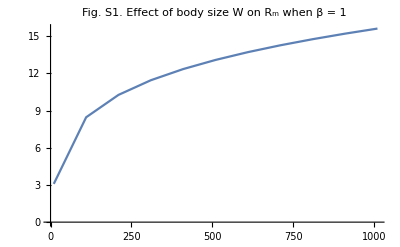
-Graphics-Host mass WGeneralist R_m

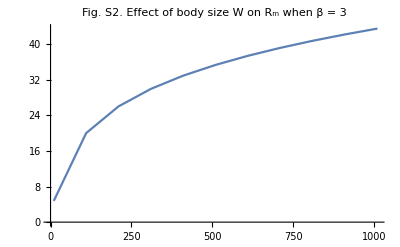
-Graphics-Host mass WGeneralist R_m

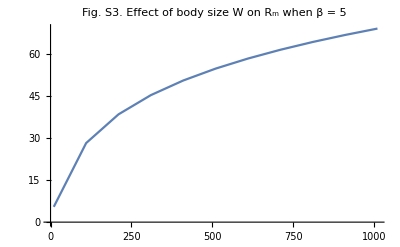
-Graphics-Host mass WGeneralist R_m

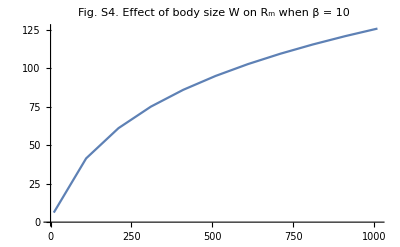
-Graphics-Host mass WGeneralist R_m

```mathematica
Wvals=Table[W,{W,10,1010,100}];
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[1,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S1. Effect of body size W on R_m when β = 1"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[3,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S2. Effect of body size W on R_m when β = 3"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[5,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S3. Effect of body size W on R_m when β = 5"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[10,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S4. Effect of body size W on R_m when β = 10"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

We can also compute the value of R_m, varying host body size W and the parasite loss rate from the environment γ.

```mathematica
(* Compute Rm for a range of W and γ values *)
RmAcrossWg=Table[Table[RmV/.{β->1,γ->g,W->Wval,T->270,a->0.8,f->0.8},{Wval,10,1010,100}],{g,0.01,1.01,0.1}];
```

Increasing host body size increases R_m, regardless of the value of γ, thereby making it easier for the generalist to invade. This can been seen in Figs. S5-S8 below.

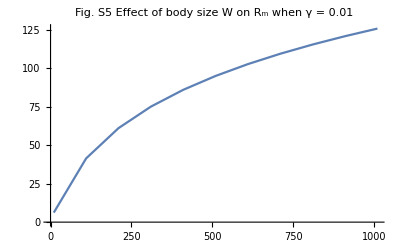
-Graphics-Host mass WGeneralist R_m

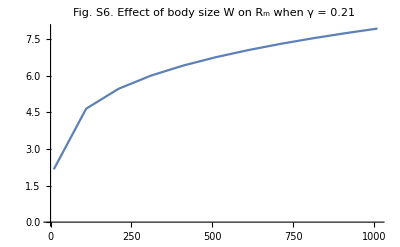
-Graphics-Host mass WGeneralist R_m

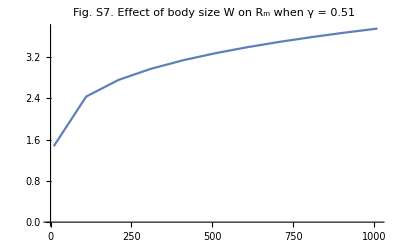
-Graphics-Host mass WGeneralist R_m

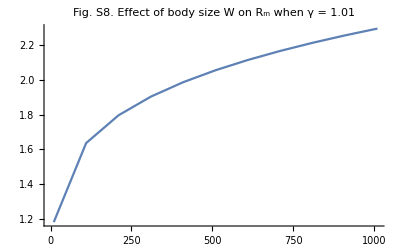
-Graphics-Host mass WGeneralist R_m

```mathematica
Wvals=Table[W,{W,10,1010,100}];
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[1,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S5 Effect of body size W on R_m when γ = 0.01"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[3,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S6. Effect of body size W on R_m when γ = 0.21"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[6,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S7. Effect of body size W on R_m when γ = 0.51"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[11,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S8. Effect of body size W on R_m when γ = 1.01"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

We can also compute the value of R_m, varying host body size W and the temperature T.

```mathematica
(* Compute Rm for a range of W and T values *)
RmAcrossWT=Table[Table[RmV/.{β->1,γ->0.2,W->Wval,T->Tval,a->0.8,f->0.8},{Tval,270,310,2}],{Wval,10,1010,100}];
```

Increasing temperature decreases R_m, regardless of host mass, thus making it more difficult for the generalist endoparasite to invade. This can be seen in Figs. S9-S12 below.

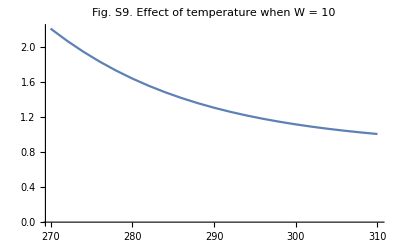
-Graphics-TemperatureGeneralist R_m

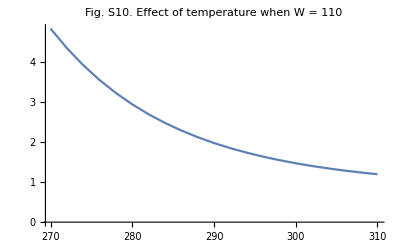
-Graphics-TemperatureGeneralist R_m

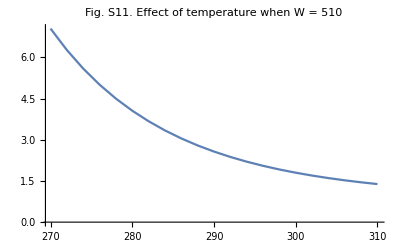
-Graphics-TemperatureGeneralist R_m

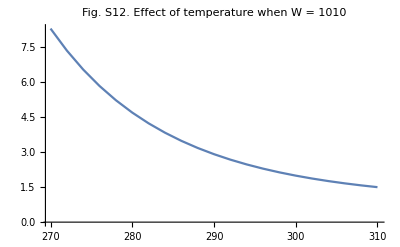
-Graphics-TemperatureGeneralist R_m

```mathematica
Tvals=Table[T,{T,270,310,2}];
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[1,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S9. Effect of temperature when W = 10"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[2,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S10. Effect of temperature when W = 110"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[6,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S11. Effect of temperature when W = 510"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[11,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S12. Effect of temperature when W = 1010"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

#### Ectoparasites:

The only change from the endoparasite case is with the scaling of λ:

```mathematica
allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(5/12),λ2->λ0 Exp[-Ε/(k T)] (f W)^(5/12),r1->r0 Exp[-Ε/(k T)] W^(-1/4),r2->r0 Exp[-Ε/(k T)] (f W)^(-1/4)};
allompars={Ε->0.43,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10};
```

We compute the value of R_m, varying host body size W and the contact rate β.

```mathematica
(* Rm, plugging in the parameter values from Table 1, the equilibria calculated above, the allometric scaling relationships, and the parameters of the allometric functions *)
RmV=Rm/.S1Eq[[1]]/.I1sEq[[1]]/.D1ssEq[[1]]/.P1Eq[[2]]/.S2->K2/.{σC1->1,βD1->0,D2ss->0,x1->1/2,I2s->0,P2->0,βS1->β,βI1->β,βS2->β}/.allom/.allompars;
(* Compute Rm for a range of W and β values *)
RmAcrossWB=Table[Table[RmV/.{β->B,γ->0.1,W->Wval,T->270,a->0.8,f->0.8},{Wval,10,1010,100}],{B,1,10,1}];
```

The relationship between host body size and R_m depends on the value of β. For very low β, the generalist cannot invade. For values of β large enough to permit the generalist to invade, increasing host body size first increases, then decreases, R_m. Note that this is the same response as was the case for the model without coinfection. This can be seen in Figs. S13-S16 below.

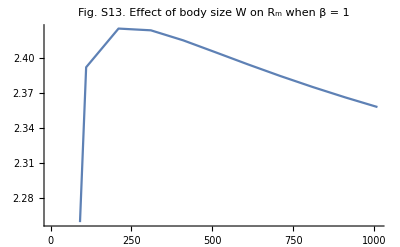
-Graphics-Host mass WGeneralist R_m

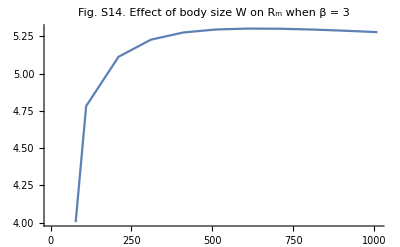
-Graphics-Host mass WGeneralist R_m

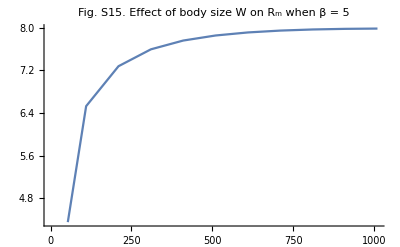
-Graphics-Host mass WGeneralist R_m

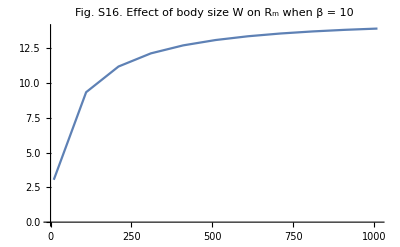
-Graphics-Host mass WGeneralist R_m

```mathematica
Wvals=Table[W,{W,10,1010,100}];
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[1,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S13. Effect of body size W on R_m when β = 1"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[3,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S14. Effect of body size W on R_m when β = 3"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[5,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S15. Effect of body size W on R_m when β = 5"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[10,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S16. Effect of body size W on R_m when β = 10"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

We can also compute the value of R_m, varying host body size W and the temperature T to determine the effect of temperature.

```mathematica
(* Compute Rm for a range of W and T values *)
RmAcrossWT=Table[Table[RmV/.{β->0.5,γ->0.1,W->Wval,T->Tval,a->0.8,f->0.8},{Tval,270,310,2}],{Wval,10,1010,100}];
```

Increasing temperature decreases R_m, regardless of host mass, thus making it more difficult for the generalist endoparasite to invade. This can be seen in Figs. S17-S20 below.

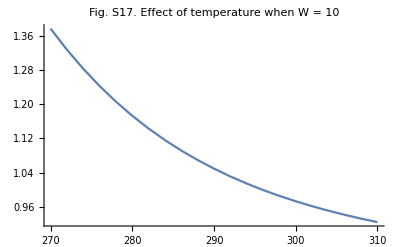
-Graphics-TemperatureGeneralist R_m

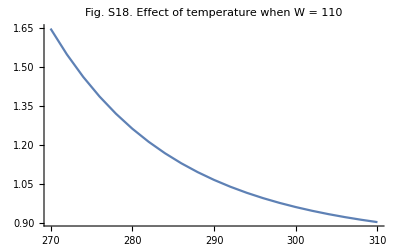
-Graphics-TemperatureGeneralist R_m

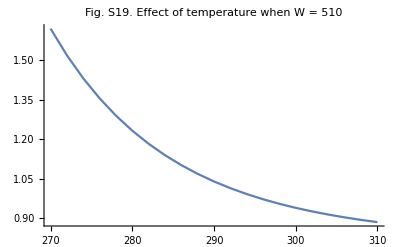
-Graphics-TemperatureGeneralist R_m

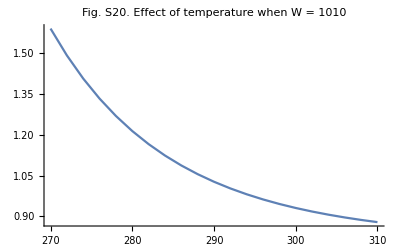
-Graphics-TemperatureGeneralist R_m

```mathematica
Tvals=Table[T,{T,270,310,2}];
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[1,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S17. Effect of temperature when W = 10"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[2,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S18. Effect of temperature when W = 110"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[6,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S19. Effect of temperature when W = 510"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[11,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S20. Effect of temperature when W = 1010"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

### Two specialist parasites, with coinfection, with avoidance of non-susceptible hosts

Based on the parameters presented in Table 1 in the main text, the R_m expression will is nearly identical to Eqn. 12 in the main text: R_m=(β_S_1 OverHat[S_1])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+β_I_2 OverHat[I_(2,s)]+γ) (μ_1/(μ_1+β_I_1 OverHat[P_1]) (a λ_1)/μ_1+(β_I_1 OverHat[P_1])/(μ_1+β_I_1 OverHat[P_1]) (a (1-x_1)λ_1)/μ_1)+(β_I_1 OverHat[I_(1,s)])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+β_I_2 OverHat[I_(2,s)]+γ)(a (1-x_1)λ_1)/μ_1+(β_S_2 OverHat[S_2])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+β_I_2 OverHat[I_(2,s)]+γ) (μ_2/(μ_2+β_I_2 OverHat[P_2]) (a λ_2)/μ_2+(β_I_2 OverHat[P_2])/(μ_2+β_I_2 OverHat[P_2]) (a (1-x_2)λ_2)/μ_2)+(β_I_2 OverHat[I_(2,s)])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+β_I_2 OverHat[I_(2,s)]+γ)(a (1-x_2)λ_2)/μ_2 >1.

The generalized R_m expression for any number of hosts (Eq. 12 in the main text) follows from this expression.

Based on the parameters presented in Table 1 in the main text, the R_m expression will simplify to the expression R_m=(β_S_1 OverHat[S_1])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+γ) (μ_1/(μ_1+β_I_1 OverHat[P_1]) (a λ_1)/μ_1+(β_I_1 OverHat[P_1])/(μ_1+β_I_1 OverHat[P_1]) (a (1-x_1)λ_1)/μ_1)+(β_I_1 OverHat[I_(1,s)])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+γ)(a (1-x_1)λ_1)/μ_1+(β_S_2 OverHat[S_2])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+γ) ( (a λ_2)/μ_2). 
The parasite can invade if R_m>1. 

Unfortunately, it is analytically intractable to determine the sign of (∂R_m)/(∂W) or (∂R_m)/(∂T), so we use numerical exploration to determine the effect of host body size and environmental temperature on the R_m.

```mathematica
(* Rm at the parameters for this case from Table 1 *)
Rm/.{βD1->0,βD2->0,σC1->1,σC2->1}
```

(a I1s (1-x1) βI1 λ1)/((I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1)+(S1 βS1 ((a λ1)/(P1 βI1+μ1)+(a P1 (1-x1) βI1 λ1)/(μ1 (P1 βI1+μ1))))/(I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ)+(a I2s (1-x2) βI2 λ2)/((I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ2)+(S2 βS2 ((a λ2)/(P2 βI2+μ2)+(a P2 (1-x2) βI2 λ2)/(μ2 (P2 βI2+μ2))))/(I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ)

#### Endoparasites:

Many of the parameters of the model are set by allometric relationships and have been established previously (Gillooly et al. 2001, Allen et al. 2002, Savage et al. 2004, Poulin & George-Nascimento 2007).

```mathematica
allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4),r1->r0 Exp[-Ε/(k T)] W^(-1/4),r2->r0 Exp[-Ε/(k T)] (f W)^(-1/4)};
allompars={Ε->0.43,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10};
```

That leaves a much smaller subset of parameters that can be varied. For simplicity, we focus on parameters whose effects on invasion fitness are complex. This excludes parameters related to the costs associated with generalism, including a (the reduction in shedding rate for generalists), σ_C_1 (the probability of coinfection, which we hold constant at 1), and x_1 (the fraction of host resources captured by the resident strains in coinfection, which we hold constant at 1/2). None of these parameters affect the equilibrium abundances of susceptible and singly infected hosts, so their effect on R_m are predictable and obvious - reducing a, reducing σ_C_1, or increasing x_1 will all reduce R_m, making invasion by the generalist more difficult. Thus the only parameters to explore (other than host mass W and temperature T), are the contact rates between hosts and parasites and γ (the loss rate of parasites from the environment). For simplicity, we assume that all contact rates are equal (β_S_1=β_I_1=β_S_2=β).

We can solve for the equilibria analytically, although the expression for OverHat[P_1] and OverHat[P_2]cannot be expressed simply.

```mathematica
(* Solving for Subscript[S, 1] in terms of Subscript[I, 1,s] and Subscript[P, 1]*)
S1Eq=Solve[(dI1sdt/.{σC1->1,σD1->1,Pg->0})==0,S1];
(* Solving for Subscript[I, 1,s] in terms of Subscript[D, 1,s,s] and Subscript[P, 1] *)
I1sEq=Solve[(dD1ssdt/.σD1->1)==0,I1s];
(* Solving for Subscript[D, 1,s,s] in terms of Subscript[P, 1] *)
D1ssEq=Simplify[Solve[(dP1dt/.{βC1->0,βD1->0,C1sg->0}/.S1Eq[[1]]/.I1sEq[[1]])==0,D1ss]]
(* Solving for Subscript[I, 1,s] in terms of Subscript[P, 1] *)
I1sEq=Simplify[I1sEq/.D1ssEq[[1]]]
(* Solving for Subscript[S, 1] in terms of Subscript[P, 1] *)
S1Eq=Simplify[S1Eq/.I1sEq[[1]]]
(* Solving for Subscript[P, 1] *)
P1Eq=Solve[Simplify[dS1dt/.{C1sg->0,I1g->0,Pg->0}/.S1Eq[[1]]/.I1sEq[[1]]/.D1ssEq[[1]]]==0,P1];
(* Solving for Subscript[S, 2] in terms of Subscript[I, 2,s] and Subscript[P, 2]*)
S2Eq=Solve[(dI2sdt/.{σC2->1,σD2->1,Pg->0})==0,S2];
(* Solving for Subscript[I, 2,s] in terms of Subscript[D, 2,s,s] and Subscript[P, 2] *)
I2sEq=Solve[(dD2ssdt/.σD2->1)==0,I2s];
(* Solving for Subscript[D, 2,s,s] in terms of Subscript[P, 2] *)
D2ssEq=Simplify[Solve[(dP2dt/.{βC2->0,βD2->0,C2sg->0}/.S2Eq[[1]]/.I2sEq[[1]])==0,D2ss]]
(* Solving for Subscript[I, 2,s] in terms of Subscript[P, 2] *)
I2sEq=Simplify[I2sEq/.D2ssEq[[1]]]
(* Solving for Subscript[S, 2] in terms of Subscript[P, 2] *)
S2Eq=Simplify[S2Eq/.I2sEq[[1]]]
(* Solving for Subscript[P, 2] *)
P2Eq=Solve[Simplify[dS2dt/.{C2sg->0,I2g->0,Pg->0}/.S2Eq[[1]]/.I2sEq[[1]]/.D2ssEq[[1]]]==0,P2];
```

{{D1ss→(P1^2 βI1 γ)/(P1 βI1 (λ1-2 μ1)+(λ1-μ1) μ1)}}

{{I1s→(P1 γ μ1)/(P1 βI1 (λ1-2 μ1)+(λ1-μ1) μ1)}}

{{S1→(γ μ1 (P1 βI1+μ1))/(βS1 (P1 βI1 (λ1-2 μ1)+(λ1-μ1) μ1))}}

{{D2ss→(P2^2 βI2 γ)/(P2 βI2 (λ2-2 μ2)+(λ2-μ2) μ2)}}

{{I2s→(P2 γ μ2)/(P2 βI2 (λ2-2 μ2)+(λ2-μ2) μ2)}}

{{S2→(γ μ2 (P2 βI2+μ2))/(βS2 (P2 βI2 (λ2-2 μ2)+(λ2-μ2) μ2))}}

With these equilibria, we can compute the value of R_m, varying host body size W and the contact rate β.

```mathematica
(* Rm, plugging in the parameter values from Table 1, the equilibria calculated above, the allometric scaling relationships, and the parameters of the allometric functions *)
RmV=Rm/.S1Eq[[1]]/.I1sEq[[1]]/.D1ssEq[[1]]/.P1Eq[[2]]/.S2Eq[[1]]/.I2sEq[[1]]/.D2ssEq[[1]]/.P2Eq[[2]]/.{σC1->1,σC2->1,βD1->0,βD2->0,x1->1/2,x2->1/2,βS1->β,βI1->β,βS2->β,βI2->β}/.allom/.allompars;
(* Compute Rm for a range of W and β values *)
RmAcrossWB=Table[Table[RmV/.{β->B,γ->0.1,W->Wval,T->270,a->0.8,f->0.8},{Wval,10,1010,100}],{B,1,10,1}];
```

Increasing host body size increases R_m, regardless of the value of β, thereby making it easier for the generalist to invade. This can be seen in Figs. S21-S24 below.

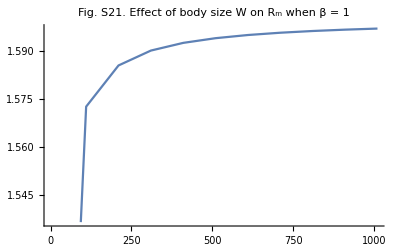
-Graphics-Host mass WGeneralist R_m

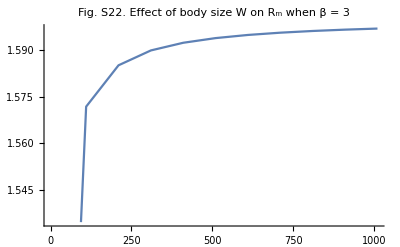
-Graphics-Host mass WGeneralist R_m

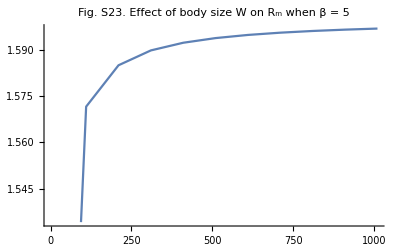
-Graphics-Host mass WGeneralist R_m

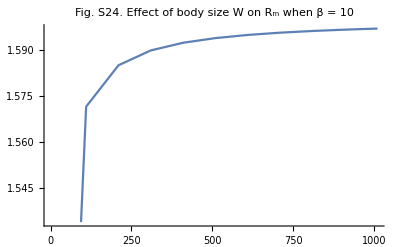
-Graphics-Host mass WGeneralist R_m

```mathematica
Wvals=Table[W,{W,10,1010,100}];
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[1,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S21. Effect of body size W on R_m when β = 1"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[3,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S22. Effect of body size W on R_m when β = 3"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[5,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S23. Effect of body size W on R_m when β = 5"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[10,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S24. Effect of body size W on R_m when β = 10"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

We can also compute the value of R_m, varying host body size W and the parasite loss rate from the environment γ.

```mathematica
(* Compute Rm for a range of W and γ values *)
RmAcrossWg=Table[Table[RmV/.{β->1,γ->g,W->Wval,T->270,a->0.8,f->0.8},{Wval,10,1010,100}],{g,0.01,1.01,0.1}];
```

Increasing host body size increases R_m, regardless of the value of γ, thereby making it easier for the generalist to invade. This can been seen in Figs. S25-S28 below.

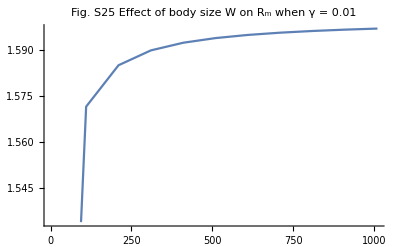
-Graphics-Host mass WGeneralist R_m

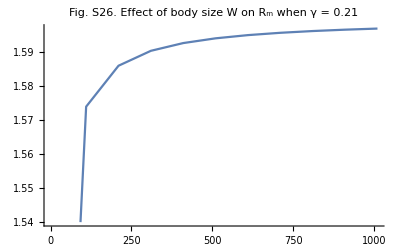
-Graphics-Host mass WGeneralist R_m

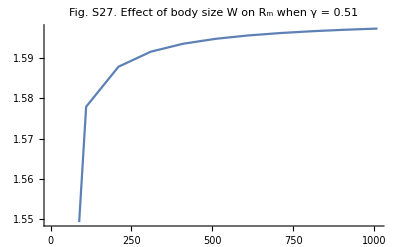
-Graphics-Host mass WGeneralist R_m

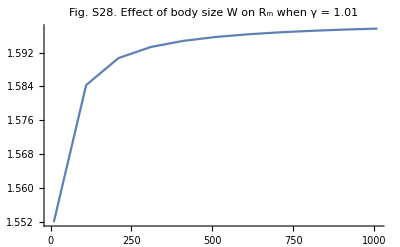
-Graphics-Host mass WGeneralist R_m

```mathematica
Wvals=Table[W,{W,10,1010,100}];
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[1,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S25 Effect of body size W on R_m when γ = 0.01"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[3,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S26. Effect of body size W on R_m when γ = 0.21"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[6,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S27. Effect of body size W on R_m when γ = 0.51"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[11,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S28. Effect of body size W on R_m when γ = 1.01"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

We can also compute the value of R_m, varying host body size W and the temperature T.

```mathematica
(* Compute Rm for a range of W and T values *)
RmAcrossWT=Table[Table[RmV/.{β->1,γ->0.2,W->Wval,T->Tval,a->0.8,f->0.8},{Tval,270,310,2}],{Wval,10,1010,100}];
```

Increasing temperature increases R_m, although the increase is very slight, and as host mass increases, the increase in R_m with temperature gets shallower. This can be seen in Figs. S29-S32 below.

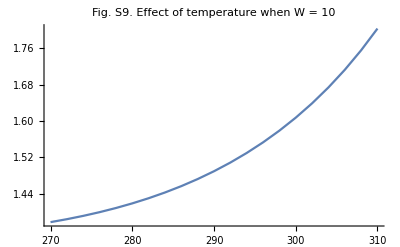
-Graphics-TemperatureGeneralist R_m

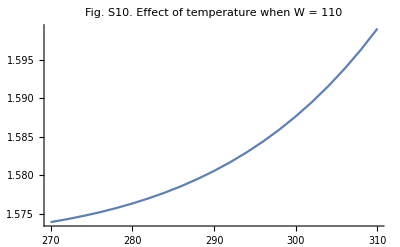
-Graphics-TemperatureGeneralist R_m

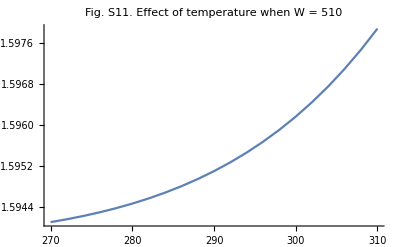
-Graphics-TemperatureGeneralist R_m

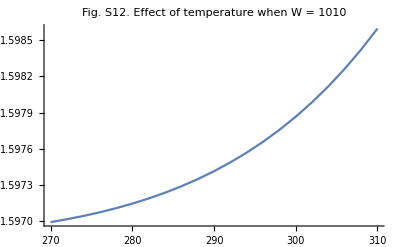
-Graphics-TemperatureGeneralist R_m

```mathematica
Tvals=Table[T,{T,270,310,2}];
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[1,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S9. Effect of temperature when W = 10"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[2,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S10. Effect of temperature when W = 110"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[6,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S11. Effect of temperature when W = 510"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[11,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S12. Effect of temperature when W = 1010"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

#### Ectoparasites:

All that needs to be changed from the previous case is the scaling of λ with body size.

```mathematica
allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(5/12),λ2->λ0 Exp[-Ε/(k T)] (f W)^(5/12),r1->r0 Exp[-Ε/(k T)] W^(-1/4),r2->r0 Exp[-Ε/(k T)] (f W)^(-1/4)};
allompars={Ε->0.43,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10};
```

We can compute the value of R_m, varying host body size W and the contact rate β.

```mathematica
(* Rm, plugging in the parameter values from Table 1, the equilibria calculated above, the allometric scaling relationships, and the parameters of the allometric functions *)
RmV=Rm/.S1Eq[[1]]/.I1sEq[[1]]/.D1ssEq[[1]]/.P1Eq[[2]]/.S2Eq[[1]]/.I2sEq[[1]]/.D2ssEq[[1]]/.P2Eq[[2]]/.{σC1->1,σC2->1,βD1->0,βD2->0,x1->1/2,x2->1/2,βS1->β,βI1->β,βS2->β,βI2->β}/.allom/.allompars;
(* Compute Rm for a range of W and β values *)
RmAcrossWB=Table[Table[RmV/.{β->B,γ->0.1,W->Wval,T->270,a->0.8,f->0.8},{Wval,10,1010,100}],{B,1,10,1}];
```

Increasing host body size increases R_m, regardless of the value of β, thereby making it easier for the generalist to invade. This can be seen in Figs. S33-S36 below.

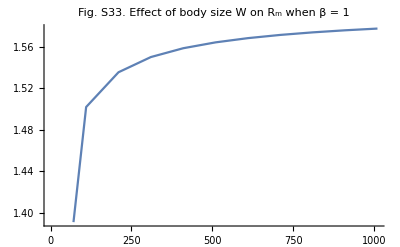
-Graphics-Host mass WGeneralist R_m

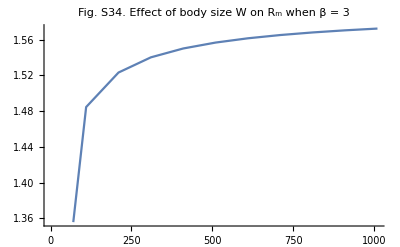
-Graphics-Host mass WGeneralist R_m

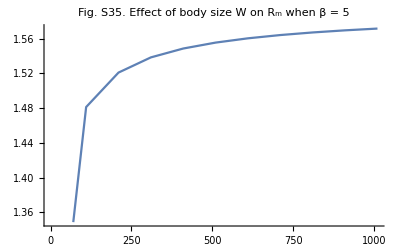
-Graphics-Host mass WGeneralist R_m

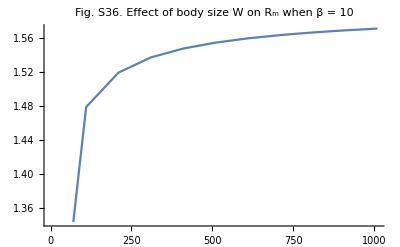
-Graphics-Host mass WGeneralist R_m

```mathematica
Wvals=Table[W,{W,10,1010,100}];
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[1,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S33. Effect of body size W on R_m when β = 1"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[3,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S34. Effect of body size W on R_m when β = 3"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[5,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S35. Effect of body size W on R_m when β = 5"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[10,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S36. Effect of body size W on R_m when β = 10"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

We can also compute the value of R_m, varying host body size W and the parasite loss rate from the environment γ.

```mathematica
(* Compute Rm for a range of W and γ values *)
RmAcrossWg=Table[Table[
RmV/.{β->1,γ->g,W->Wval,T->270,a->0.8,f->0.8},{Wval,10,1010,100}],{g,0.01,0.1,0.01}];
```

Increasing host body size increases R_m, regardless of the value of γ, thereby making it easier for the generalist to invade. This can been seen in Figs. S37-S40 below.

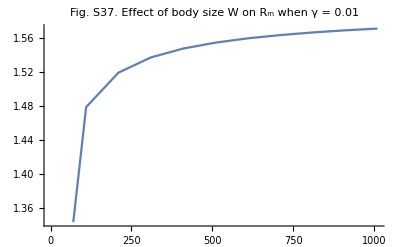
-Graphics-Host mass WGeneralist R_m

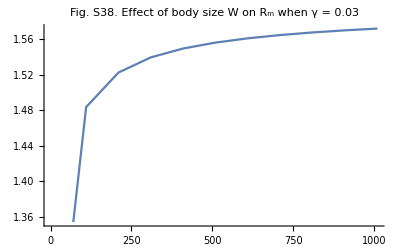
-Graphics-Host mass WGeneralist R_m

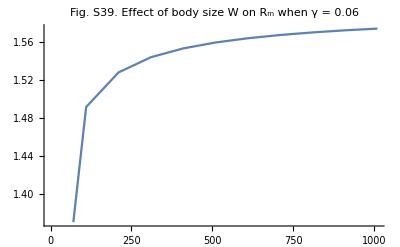
-Graphics-Host mass WGeneralist R_m

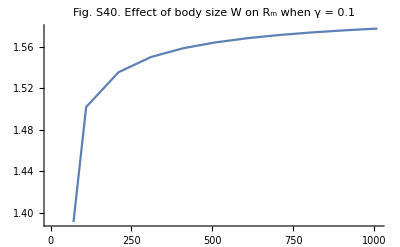
-Graphics-Host mass WGeneralist R_m

```mathematica
Wvals=Table[W,{W,10,1010,100}];
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[1,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S37. Effect of body size W on R_m when γ = 0.01"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[3,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S38. Effect of body size W on R_m when γ = 0.03"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[6,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S39. Effect of body size W on R_m when γ = 0.06"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[10,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S40. Effect of body size W on R_m when γ = 0.1"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

We can also compute the value of R_m, varying host body size W and the temperature T.

```mathematica
(* Compute Rm for a range of W and T values *)
RmAcrossWT=Table[Table[RmV/.{β->1,γ->0.1,W->Wval,T->Tval,a->0.8,f->0.8},{Tval,270,310,2}],{Wval,10,1010,100}];
```

Increasing temperature increases R_m, making it easier for the generalist to invade. This can be seen in Figs. S41-S44 below.

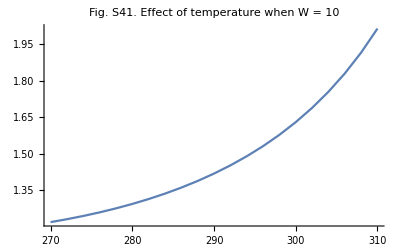
-Graphics-TemperatureGeneralist R_m

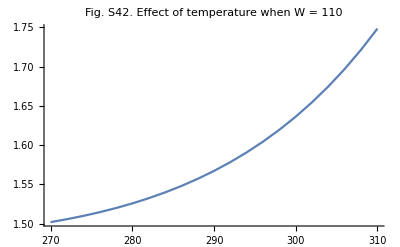
-Graphics-TemperatureGeneralist R_m

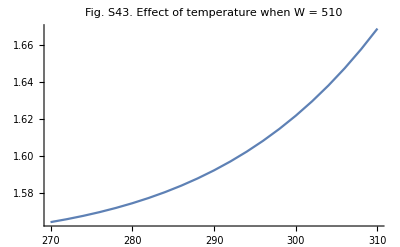
-Graphics-TemperatureGeneralist R_m

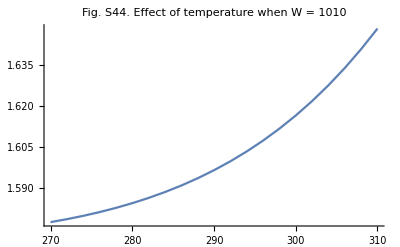
-Graphics-TemperatureGeneralist R_m

```mathematica
Tvals=Table[T,{T,270,310,2}];
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[1,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S41. Effect of temperature when W = 10"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[2,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S42. Effect of temperature when W = 110"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[6,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S43. Effect of temperature when W = 510"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[11,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S44. Effect of temperature when W = 1010"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

### Two specialist parasites, with coinfection, with no avoidance of non-susceptible hosts

The R_m expression cannot be simplifed at all from the form presented in Eqn. 12 in the main text. 

However, we can solve for OverHat[S_1], OverHat[I_(1,s)],OverHat[D_(1,s,s)] in terms of OverHat[P_1] and OverHat[S_2], OverHat[I_(2,s)],OverHat[D_(2,s,s)] in terms of OverHat[P_2].

```mathematica
Solve[(dP1dt/.{C1sg->0}/.{S1->(I1s P1 βI1+I1s μ1)/(P1 βS1)}/.{I1s->(D1ss μ1)/(P1 βI1)})==0,D1ss]//Simplify
```

{{D1ss→-(P1^2 βI1 γ)/(P1^2 βD1 βI1-P1 βI1 λ1+2 P1 βI1 μ1-λ1 μ1+μ1^2)}}

```mathematica
(* Solving for Subscript[S, 1] in terms of Subscript[I, 1,s] and Subscript[P, 1]*)
S1Eq=Solve[(dI1sdt/.{σC1->1,σD1->1,Pg->0})==0,S1];
(* Solving for Subscript[I, 1,s] in terms of Subscript[D, 1,s,s] and Subscript[P, 1] *)
I1sEq=Solve[(dD1ssdt/.σD1->1)==0,I1s];
(* Solving for Subscript[D, 1,s,s] in terms of Subscript[P, 1] *)
D1ssEq=Simplify[Solve[(dP1dt/.{C1sg->0}/.S1Eq[[1]]/.I1sEq[[1]])==0,D1ss]]
(* Solving for Subscript[I, 1,s] in terms of Subscript[P, 1] *)
I1sEq=Simplify[I1sEq/.D1ssEq[[1]]]
(* Solving for Subscript[S, 1] in terms of Subscript[P, 1] *)
S1Eq=Simplify[S1Eq/.I1sEq[[1]]]
(* Solving for Subscript[P, 1] *)
P1Eq=Solve[Simplify[dS1dt/.{C1sg->0,I1g->0,Pg->0}/.S1Eq[[1]]/.I1sEq[[1]]/.D1ssEq[[1]]]==0,P1];
(* Solving for Subscript[S, 2] in terms of Subscript[I, 2,s] and Subscript[P, 2]*)
S2Eq=Solve[(dI2sdt/.{σC2->1,σD2->1,Pg->0})==0,S2];
(* Solving for Subscript[I, 2,s] in terms of Subscript[D, 2,s,s] and Subscript[P, 2] *)
I2sEq=Solve[(dD2ssdt/.σD2->1)==0,I2s];
(* Solving for Subscript[D, 2,s,s] in terms of Subscript[P, 2] *)
D2ssEq=Simplify[Solve[(dP2dt/.{C2sg->0}/.S2Eq[[1]]/.I2sEq[[1]])==0,D2ss]]
(* Solving for Subscript[I, 2,s] in terms of Subscript[P, 2] *)
I2sEq=Simplify[I2sEq/.D2ssEq[[1]]]
(* Solving for Subscript[S, 2] in terms of Subscript[P, 2] *)
S2Eq=Simplify[S2Eq/.I2sEq[[1]]]
(* Solving for Subscript[P, 2] *)
P2Eq=Solve[Simplify[dS2dt/.{C2sg->0,I2g->0,Pg->0}/.S2Eq[[1]]/.I2sEq[[1]]/.D2ssEq[[1]]]==0,P2];
```

{{D1ss→-(P1^2 βI1 γ)/(P1^2 βD1 βI1-P1 βI1 λ1+2 P1 βI1 μ1-λ1 μ1+μ1^2)}}

{{I1s→-(P1 γ μ1)/(P1^2 βD1 βI1-P1 βI1 λ1+2 P1 βI1 μ1-λ1 μ1+μ1^2)}}

{{S1→-(γ μ1 (P1 βI1+μ1))/(βS1 (P1^2 βD1 βI1-P1 βI1 (λ1-2 μ1)+μ1 (-λ1+μ1)))}}

{{D2ss→-(P2^2 βI2 γ)/(P2^2 βD2 βI2-P2 βI2 λ2+2 P2 βI2 μ2-λ2 μ2+μ2^2)}}

{{I2s→-(P2 γ μ2)/(P2^2 βD2 βI2-P2 βI2 λ2+2 P2 βI2 μ2-λ2 μ2+μ2^2)}}

{{S2→-(γ μ2 (P2 βI2+μ2))/(βS2 (P2^2 βD2 βI2-P2 βI2 (λ2-2 μ2)+μ2 (-λ2+μ2)))}}

If we plug these equilibria into the expression for R_m, we can simplify it considerably, if we also make the assumption that x_1=x_2=0.5, σ_C_1=σ_C_2=1, and β_I_1=β_I_2=β_D_1=β_D_2=β.

```mathematica
(* Simplifying the expression for Subscript[R, m] *)
Simplify[Rm/.S1Eq[[1]]/.I1sEq[[1]]/.D1ssEq[[1]]/.S2Eq[[1]]/.I2sEq[[1]]/.D2ssEq[[1]]/.{x1->1/2,x2->1/2,σC1->1,σC2->1,βI1->β,βI2->β,βD1->β,βD2->β}]
```

(a (P2 β λ1+P1 β λ2-2 λ1 λ2+λ2 μ1+λ1 μ2))/(-λ1 λ2+P1 β (P2 β+μ2)+μ1 (P2 β+μ2))

The generalist can only invade if the numerator is larger than then denominator when a=1. This is only true if (β OverHat[P_1]-λ_1+μ_1)(β OverHat[P_2]-λ_2+μ_2)<0. But both of these expressions must be negative to guarantee the positivity of OverHat[S_1] and OverHat[S_2], which means that the generalist can never invade.

```mathematica
(* Is the numerator ever larger than the denominator? This requires the following to be true *)
Simplify[Expand[(P2 β λ1+P1 β λ2-2 λ1 λ2+λ2 μ1+λ1 μ2)>-λ1 λ2+P1 β (P2 β+μ2)+μ1 (P2 β+μ2)]]
```

(P1 β-λ1+μ1) (P2 β-λ2+μ2)<0